# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from publication T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Documents\Simulations et calculs\Simulation_Rydberg + taille du BEC dans piège magnétique\Spectres VdW\radinte\radinte.exe",93,9]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

-0.0267742

-0.0267742

0.00740212

{0.,0.00741686}

## | 58 s1/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=57;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=52; Subscript[n, max]=67;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==Subscript[m, 1],t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
NList
```

-1.1337×10^12

{0.14,Null}

320

{{53,3,5/2,1/2,-1.1719×10^12,-1},{53,3,7/2,1/2,-1.1719×10^12,-1},{53,4,7/2,1/2,-1.17117×10^12,1},{53,4,9/2,1/2,-1.17117×10^12,1},{53,5,9/2,1/2,-1.17117×10^12,-1},{53,5,11/2,1/2,-1.17117×10^12,-1},{53,6,11/2,1/2,-1.17117×10^12,1},{53,6,13/2,1/2,-1.17117×10^12,1},{53,7,13/2,1/2,-1.17117×10^12,-1},{53,7,15/2,1/2,-1.17117×10^12,-1},{53,8,15/2,1/2,-1.17117×10^12,1},{53,8,17/2,1/2,-1.17117×10^12,1},{53,9,17/2,1/2,-1.17117×10^12,-1},{53,9,19/2,1/2,-1.17117×10^12,-1},{53,10,19/2,1/2,-1.17117×10^12,1},{53,10,21/2,1/2,-1.17117×10^12,1},{53,11,21/2,1/2,-1.17117×10^12,-1},{53,11,23/2,1/2,-1.17117×10^12,-1},{53,12,23/2,1/2,-1.17117×10^12,1},{53,12,25/2,1/2,-1.17117×10^12,1},{53,13,25/2,1/2,-1.17117×10^12,-1},{53,13,27/2,1/2,-1.17117×10^12,-1},{53,14,27/2,1/2,-1.17117×10^12,1},{53,14,29/2,1/2,-1.17117×10^12,1},{53,15,29/2,1/2,-1.17117×10^12,-1},{53,15,31/2,1/2,-1.17117×10^12,-1},{53,16,31/2,1/2,-1.17117×10^12,1},{53,16,33/2,1/2,-1.17117×10^12,1},{53,17,33/2,1/2,-1.17117×10^12,-1},{53,17,35/2,1/2,-1.17117×10^12,-1},{53,18,35/2,1/2,-1.17117×10^12,1},{53,18,37/2,1/2,-1.17117×10^12,1},{53,19,37/2,1/2,-1.17117×10^12,-1},{53,19,39/2,1/2,-1.17117×10^12,-1},{53,20,39/2,1/2,-1.17117×10^12,1},{53,20,41/2,1/2,-1.17117×10^12,1},{53,21,41/2,1/2,-1.17117×10^12,-1},{53,21,43/2,1/2,-1.17117×10^12,-1},{53,22,43/2,1/2,-1.17117×10^12,1},{53,22,45/2,1/2,-1.17117×10^12,1},{53,23,45/2,1/2,-1.17117×10^12,-1},{53,23,47/2,1/2,-1.17117×10^12,-1},{53,24,47/2,1/2,-1.17117×10^12,1},{53,24,49/2,1/2,-1.17117×10^12,1},{53,25,49/2,1/2,-1.17117×10^12,-1},{53,25,51/2,1/2,-1.17117×10^12,-1},{53,26,51/2,1/2,-1.17117×10^12,1},{53,26,53/2,1/2,-1.17117×10^12,1},{53,27,53/2,1/2,-1.17117×10^12,-1},{53,27,55/2,1/2,-1.17117×10^12,-1},{53,28,55/2,1/2,-1.17117×10^12,1},{53,28,57/2,1/2,-1.17117×10^12,1},{53,29,57/2,1/2,-1.17117×10^12,-1},{53,29,59/2,1/2,-1.17117×10^12,-1},{53,30,59/2,1/2,-1.17117×10^12,1},{53,30,61/2,1/2,-1.17117×10^12,1},{53,31,61/2,1/2,-1.17117×10^12,-1},{53,31,63/2,1/2,-1.17117×10^12,-1},{53,32,63/2,1/2,-1.17117×10^12,1},{53,32,65/2,1/2,-1.17117×10^12,1},{53,33,65/2,1/2,-1.17117×10^12,-1},{53,33,67/2,1/2,-1.17117×10^12,-1},{53,34,67/2,1/2,-1.17117×10^12,1},{53,34,69/2,1/2,-1.17117×10^12,1},{53,35,69/2,1/2,-1.17117×10^12,-1},{53,35,71/2,1/2,-1.17117×10^12,-1},{53,36,71/2,1/2,-1.17117×10^12,1},{53,36,73/2,1/2,-1.17117×10^12,1},{53,37,73/2,1/2,-1.17117×10^12,-1},{53,37,75/2,1/2,-1.17117×10^12,-1},{53,38,75/2,1/2,-1.17117×10^12,1},{53,38,77/2,1/2,-1.17117×10^12,1},{53,39,77/2,1/2,-1.17117×10^12,-1},{53,39,79/2,1/2,-1.17117×10^12,-1},{53,40,79/2,1/2,-1.17117×10^12,1},{53,40,81/2,1/2,-1.17117×10^12,1},{53,41,81/2,1/2,-1.17117×10^12,-1},{53,41,83/2,1/2,-1.17117×10^12,-1},{53,42,83/2,1/2,-1.17117×10^12,1},{53,42,85/2,1/2,-1.17117×10^12,1},{53,43,85/2,1/2,-1.17117×10^12,-1},{53,43,87/2,1/2,-1.17117×10^12,-1},{53,44,87/2,1/2,-1.17117×10^12,1},{53,44,89/2,1/2,-1.17117×10^12,1},{53,45,89/2,1/2,-1.17117×10^12,-1},{53,45,91/2,1/2,-1.17117×10^12,-1},{53,46,91/2,1/2,-1.17117×10^12,1},{53,46,93/2,1/2,-1.17117×10^12,1},{53,47,93/2,1/2,-1.17117×10^12,-1},{53,47,95/2,1/2,-1.17117×10^12,-1},{53,48,95/2,1/2,-1.17117×10^12,1},{53,48,97/2,1/2,-1.17117×10^12,1},{53,49,97/2,1/2,-1.17117×10^12,-1},{53,49,99/2,1/2,-1.17117×10^12,-1},{53,50,99/2,1/2,-1.17117×10^12,1},{53,50,101/2,1/2,-1.17117×10^12,1},{53,51,101/2,1/2,-1.17117×10^12,-1},{53,51,103/2,1/2,-1.17117×10^12,-1},{53,52,103/2,1/2,-1.17117×10^12,1},{53,52,105/2,1/2,-1.17117×10^12,1},{54,2,3/2,1/2,-1.1867×10^12,1},{54,2,5/2,1/2,-1.18663×10^12,1},{54,3,5/2,1/2,-1.12889×10^12,-1},{54,3,7/2,1/2,-1.12889×10^12,-1},{54,4,7/2,1/2,-1.1282×10^12,1},{54,4,9/2,1/2,-1.1282×10^12,1},{54,5,9/2,1/2,-1.1282×10^12,-1},{54,5,11/2,1/2,-1.1282×10^12,-1},{54,6,11/2,1/2,-1.1282×10^12,1},{54,6,13/2,1/2,-1.1282×10^12,1},{54,7,13/2,1/2,-1.1282×10^12,-1},{54,7,15/2,1/2,-1.1282×10^12,-1},{54,8,15/2,1/2,-1.1282×10^12,1},{54,8,17/2,1/2,-1.1282×10^12,1},{54,9,17/2,1/2,-1.1282×10^12,-1},{54,9,19/2,1/2,-1.1282×10^12,-1},{54,10,19/2,1/2,-1.1282×10^12,1},{54,10,21/2,1/2,-1.1282×10^12,1},{54,11,21/2,1/2,-1.1282×10^12,-1},{54,11,23/2,1/2,-1.1282×10^12,-1},{54,12,23/2,1/2,-1.1282×10^12,1},{54,12,25/2,1/2,-1.1282×10^12,1},{54,13,25/2,1/2,-1.1282×10^12,-1},{54,13,27/2,1/2,-1.1282×10^12,-1},{54,14,27/2,1/2,-1.1282×10^12,1},{54,14,29/2,1/2,-1.1282×10^12,1},{54,15,29/2,1/2,-1.1282×10^12,-1},{54,15,31/2,1/2,-1.1282×10^12,-1},{54,16,31/2,1/2,-1.1282×10^12,1},{54,16,33/2,1/2,-1.1282×10^12,1},{54,17,33/2,1/2,-1.1282×10^12,-1},{54,17,35/2,1/2,-1.1282×10^12,-1},{54,18,35/2,1/2,-1.1282×10^12,1},{54,18,37/2,1/2,-1.1282×10^12,1},{54,19,37/2,1/2,-1.1282×10^12,-1},{54,19,39/2,1/2,-1.1282×10^12,-1},{54,20,39/2,1/2,-1.1282×10^12,1},{54,20,41/2,1/2,-1.1282×10^12,1},{54,21,41/2,1/2,-1.1282×10^12,-1},{54,21,43/2,1/2,-1.1282×10^12,-1},{54,22,43/2,1/2,-1.1282×10^12,1},{54,22,45/2,1/2,-1.1282×10^12,1},{54,23,45/2,1/2,-1.1282×10^12,-1},{54,23,47/2,1/2,-1.1282×10^12,-1},{54,24,47/2,1/2,-1.1282×10^12,1},{54,24,49/2,1/2,-1.1282×10^12,1},{54,25,49/2,1/2,-1.1282×10^12,-1},{54,25,51/2,1/2,-1.1282×10^12,-1},{54,26,51/2,1/2,-1.1282×10^12,1},{54,26,53/2,1/2,-1.1282×10^12,1},{54,27,53/2,1/2,-1.1282×10^12,-1},{54,27,55/2,1/2,-1.1282×10^12,-1},{54,28,55/2,1/2,-1.1282×10^12,1},{54,28,57/2,1/2,-1.1282×10^12,1},{54,29,57/2,1/2,-1.1282×10^12,-1},{54,29,59/2,1/2,-1.1282×10^12,-1},{54,30,59/2,1/2,-1.1282×10^12,1},{54,30,61/2,1/2,-1.1282×10^12,1},{54,31,61/2,1/2,-1.1282×10^12,-1},{54,31,63/2,1/2,-1.1282×10^12,-1},{54,32,63/2,1/2,-1.1282×10^12,1},{54,32,65/2,1/2,-1.1282×10^12,1},{54,33,65/2,1/2,-1.1282×10^12,-1},{54,33,67/2,1/2,-1.1282×10^12,-1},{54,34,67/2,1/2,-1.1282×10^12,1},{54,34,69/2,1/2,-1.1282×10^12,1},{54,35,69/2,1/2,-1.1282×10^12,-1},{54,35,71/2,1/2,-1.1282×10^12,-1},{54,36,71/2,1/2,-1.1282×10^12,1},{54,36,73/2,1/2,-1.1282×10^12,1},{54,37,73/2,1/2,-1.1282×10^12,-1},{54,37,75/2,1/2,-1.1282×10^12,-1},{54,38,75/2,1/2,-1.1282×10^12,1},{54,38,77/2,1/2,-1.1282×10^12,1},{54,39,77/2,1/2,-1.1282×10^12,-1},{54,39,79/2,1/2,-1.1282×10^12,-1},{54,40,79/2,1/2,-1.1282×10^12,1},{54,40,81/2,1/2,-1.1282×10^12,1},{54,41,81/2,1/2,-1.1282×10^12,-1},{54,41,83/2,1/2,-1.1282×10^12,-1},{54,42,83/2,1/2,-1.1282×10^12,1},{54,42,85/2,1/2,-1.1282×10^12,1},{54,43,85/2,1/2,-1.1282×10^12,-1},{54,43,87/2,1/2,-1.1282×10^12,-1},{54,44,87/2,1/2,-1.1282×10^12,1},{54,44,89/2,1/2,-1.1282×10^12,1},{54,45,89/2,1/2,-1.1282×10^12,-1},{54,45,91/2,1/2,-1.1282×10^12,-1},{54,46,91/2,1/2,-1.1282×10^12,1},{54,46,93/2,1/2,-1.1282×10^12,1},{54,47,93/2,1/2,-1.1282×10^12,-1},{54,47,95/2,1/2,-1.1282×10^12,-1},{54,48,95/2,1/2,-1.1282×10^12,1},{54,48,97/2,1/2,-1.1282×10^12,1},{54,49,97/2,1/2,-1.1282×10^12,-1},{54,49,99/2,1/2,-1.1282×10^12,-1},{54,50,99/2,1/2,-1.1282×10^12,1},{54,50,101/2,1/2,-1.1282×10^12,1},{54,51,101/2,1/2,-1.1282×10^12,-1},{54,51,103/2,1/2,-1.1282×10^12,-1},{54,52,103/2,1/2,-1.1282×10^12,1},{54,52,105/2,1/2,-1.1282×10^12,1},{54,53,105/2,1/2,-1.1282×10^12,-1},{54,53,107/2,1/2,-1.1282×10^12,-1},{55,2,3/2,1/2,-1.14287×10^12,1},{55,2,5/2,1/2,-1.14281×10^12,1},{55,3,5/2,1/2,-1.0882×10^12,-1},{55,3,7/2,1/2,-1.0882×10^12,-1},{55,4,7/2,1/2,-1.08754×10^12,1},{55,4,9/2,1/2,-1.08754×10^12,1},{55,5,9/2,1/2,-1.08754×10^12,-1},{55,5,11/2,1/2,-1.08754×10^12,-1},{55,6,11/2,1/2,-1.08754×10^12,1},{55,6,13/2,1/2,-1.08754×10^12,1},{55,7,13/2,1/2,-1.08754×10^12,-1},{55,7,15/2,1/2,-1.08754×10^12,-1},{55,8,15/2,1/2,-1.08754×10^12,1},{55,8,17/2,1/2,-1.08754×10^12,1},{55,9,17/2,1/2,-1.08754×10^12,-1},{55,9,19/2,1/2,-1.08754×10^12,-1},{55,10,19/2,1/2,-1.08754×10^12,1},{55,10,21/2,1/2,-1.08754×10^12,1},{55,11,21/2,1/2,-1.08754×10^12,-1},{55,11,23/2,1/2,-1.08754×10^12,-1},{55,12,23/2,1/2,-1.08754×10^12,1},{55,12,25/2,1/2,-1.08754×10^12,1},{55,13,25/2,1/2,-1.08754×10^12,-1},{55,13,27/2,1/2,-1.08754×10^12,-1},{55,14,27/2,1/2,-1.08754×10^12,1},{55,14,29/2,1/2,-1.08754×10^12,1},{55,15,29/2,1/2,-1.08754×10^12,-1},{55,15,31/2,1/2,-1.08754×10^12,-1},{55,16,31/2,1/2,-1.08754×10^12,1},{55,16,33/2,1/2,-1.08754×10^12,1},{55,17,33/2,1/2,-1.08754×10^12,-1},{55,17,35/2,1/2,-1.08754×10^12,-1},{55,18,35/2,1/2,-1.08754×10^12,1},{55,18,37/2,1/2,-1.08754×10^12,1},{55,19,37/2,1/2,-1.08754×10^12,-1},{55,19,39/2,1/2,-1.08754×10^12,-1},{55,20,39/2,1/2,-1.08754×10^12,1},{55,20,41/2,1/2,-1.08754×10^12,1},{55,21,41/2,1/2,-1.08754×10^12,-1},{55,21,43/2,1/2,-1.08754×10^12,-1},{55,22,43/2,1/2,-1.08754×10^12,1},{55,22,45/2,1/2,-1.08754×10^12,1},{55,23,45/2,1/2,-1.08754×10^12,-1},{55,23,47/2,1/2,-1.08754×10^12,-1},{55,24,47/2,1/2,-1.08754×10^12,1},{55,24,49/2,1/2,-1.08754×10^12,1},{55,25,49/2,1/2,-1.08754×10^12,-1},{55,25,51/2,1/2,-1.08754×10^12,-1},{55,26,51/2,1/2,-1.08754×10^12,1},{55,26,53/2,1/2,-1.08754×10^12,1},{55,27,53/2,1/2,-1.08754×10^12,-1},{55,27,55/2,1/2,-1.08754×10^12,-1},{55,28,55/2,1/2,-1.08754×10^12,1},{55,28,57/2,1/2,-1.08754×10^12,1},{55,29,57/2,1/2,-1.08754×10^12,-1},{55,29,59/2,1/2,-1.08754×10^12,-1},{55,30,59/2,1/2,-1.08754×10^12,1},{55,30,61/2,1/2,-1.08754×10^12,1},{55,31,61/2,1/2,-1.08754×10^12,-1},{55,31,63/2,1/2,-1.08754×10^12,-1},{55,32,63/2,1/2,-1.08754×10^12,1},{55,32,65/2,1/2,-1.08754×10^12,1},{55,33,65/2,1/2,-1.08754×10^12,-1},{55,33,67/2,1/2,-1.08754×10^12,-1},{55,34,67/2,1/2,-1.08754×10^12,1},{55,34,69/2,1/2,-1.08754×10^12,1},{55,35,69/2,1/2,-1.08754×10^12,-1},{55,35,71/2,1/2,-1.08754×10^12,-1},{55,36,71/2,1/2,-1.08754×10^12,1},{55,36,73/2,1/2,-1.08754×10^12,1},{55,37,73/2,1/2,-1.08754×10^12,-1},{55,37,75/2,1/2,-1.08754×10^12,-1},{55,38,75/2,1/2,-1.08754×10^12,1},{55,38,77/2,1/2,-1.08754×10^12,1},{55,39,77/2,1/2,-1.08754×10^12,-1},{55,39,79/2,1/2,-1.08754×10^12,-1},{55,40,79/2,1/2,-1.08754×10^12,1},{55,40,81/2,1/2,-1.08754×10^12,1},{55,41,81/2,1/2,-1.08754×10^12,-1},{55,41,83/2,1/2,-1.08754×10^12,-1},{55,42,83/2,1/2,-1.08754×10^12,1},{55,42,85/2,1/2,-1.08754×10^12,1},{55,43,85/2,1/2,-1.08754×10^12,-1},{55,43,87/2,1/2,-1.08754×10^12,-1},{55,44,87/2,1/2,-1.08754×10^12,1},{55,44,89/2,1/2,-1.08754×10^12,1},{55,45,89/2,1/2,-1.08754×10^12,-1},{55,45,91/2,1/2,-1.08754×10^12,-1},{55,46,91/2,1/2,-1.08754×10^12,1},{55,46,93/2,1/2,-1.08754×10^12,1},{55,47,93/2,1/2,-1.08754×10^12,-1},{55,47,95/2,1/2,-1.08754×10^12,-1},{55,48,95/2,1/2,-1.08754×10^12,1},{55,48,97/2,1/2,-1.08754×10^12,1},{55,49,97/2,1/2,-1.08754×10^12,-1},{55,49,99/2,1/2,-1.08754×10^12,-1},{55,50,99/2,1/2,-1.08754×10^12,1},{55,50,101/2,1/2,-1.08754×10^12,1},{55,51,101/2,1/2,-1.08754×10^12,-1},{55,51,103/2,1/2,-1.08754×10^12,-1},{55,52,103/2,1/2,-1.08754×10^12,1},{55,52,105/2,1/2,-1.08754×10^12,1},{55,53,105/2,1/2,-1.08754×10^12,-1},{55,53,107/2,1/2,-1.08754×10^12,-1},{55,54,107/2,1/2,-1.08754×10^12,1},{55,54,109/2,1/2,-1.08754×10^12,1},{56,0,1/2,1/2,-1.17699×10^12,1},{56,1,1/2,1/2,-1.15607×10^12,-1},{56,1,3/2,1/2,-1.1555×10^12,-1},{56,2,3/2,1/2,-1.10143×10^12,1},{56,2,5/2,1/2,-1.10137×10^12,1},{57,0,1/2,1/2,-1.1337×10^12,1},{57,1,1/2,1/2,-1.11392×10^12,-1},{57,1,3/2,1/2,-1.11338×10^12,-1},{58,0,1/2,1/2,-1.09275×10^12,1},{58,1,1/2,1/2,-1.07403×10^12,-1}}

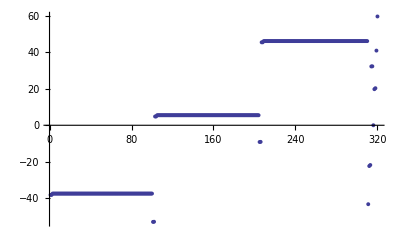

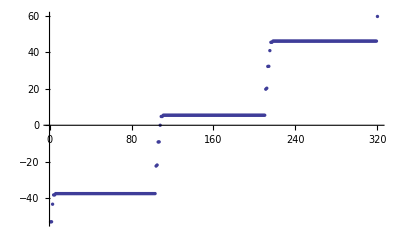

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
Calcul des éléments de matrice non-diagonaux
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.498,0.-160.498 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{14.461,Null}

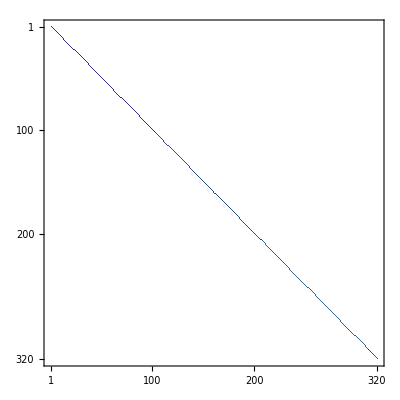

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

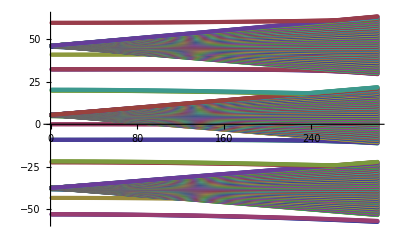

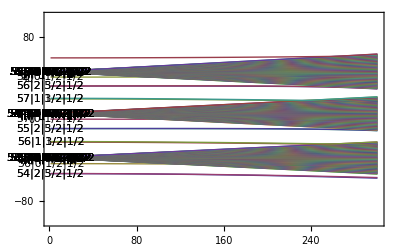

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=1;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

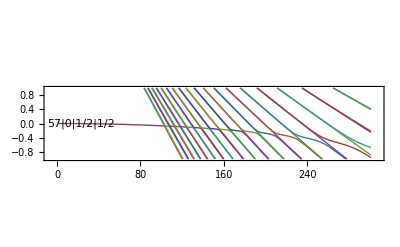

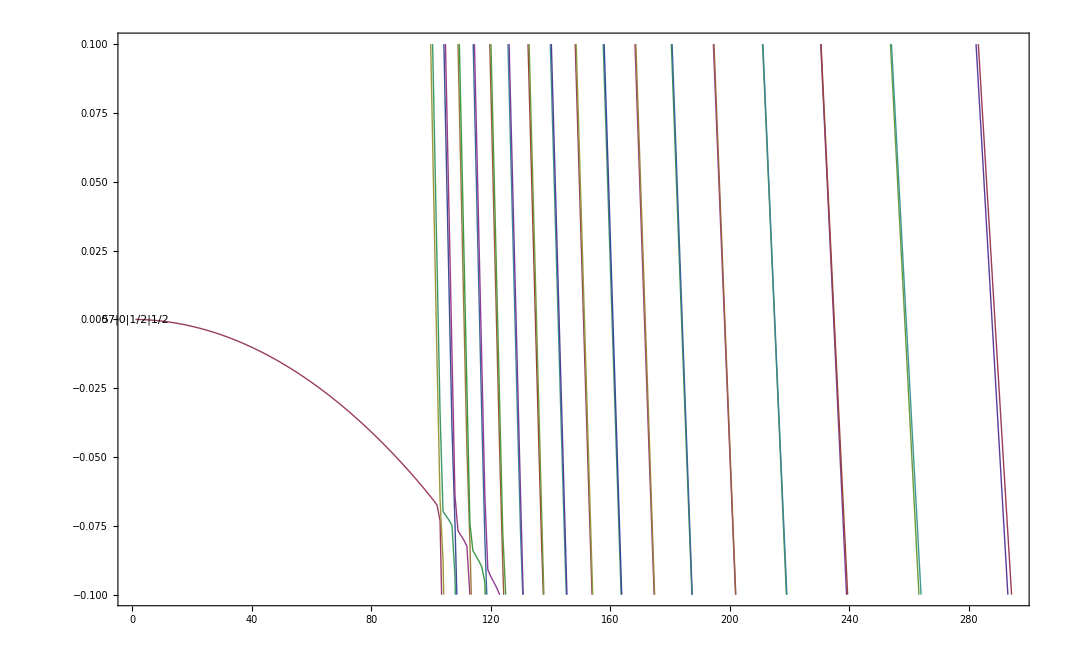

```mathematica
ELabel=1;
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-0.1,0.1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[110]]
LabelList


MPList[[110]]

Export["58s_stark_Shift.dat",MPList[[110]]]
```

58|0|1/2|1/2

{55|2|3/2|1/2,55|2|5/2|1/2,57|0|1/2|1/2,54|3|7/2|1/2,54|3|5/2|1/2,54|4|7/2|1/2,54|4|9/2|1/2,54|5|9/2|1/2,54|5|11/2|1/2,54|6|11/2|1/2,54|6|13/2|1/2,54|7|13/2|1/2,54|7|15/2|1/2,54|8|15/2|1/2,54|8|17/2|1/2,54|9|17/2|1/2,54|9|19/2|1/2,54|10|19/2|1/2,54|10|21/2|1/2,54|11|21/2|1/2,54|11|23/2|1/2,54|12|23/2|1/2,54|12|25/2|1/2,54|13|25/2|1/2,54|13|27/2|1/2,54|14|27/2|1/2,54|14|29/2|1/2,54|15|29/2|1/2,54|15|31/2|1/2,54|16|31/2|1/2,54|16|33/2|1/2,54|17|33/2|1/2,54|17|35/2|1/2,54|18|35/2|1/2,54|18|37/2|1/2,54|19|37/2|1/2,54|19|39/2|1/2,54|20|39/2|1/2,54|20|41/2|1/2,54|21|41/2|1/2,54|21|43/2|1/2,54|22|43/2|1/2,54|22|45/2|1/2,54|23|45/2|1/2,54|23|47/2|1/2,54|24|47/2|1/2,54|24|49/2|1/2,54|25|49/2|1/2,54|25|51/2|1/2,54|26|51/2|1/2,54|26|53/2|1/2,54|27|53/2|1/2,54|27|55/2|1/2,54|28|55/2|1/2,54|28|57/2|1/2,54|29|57/2|1/2,54|29|59/2|1/2,54|30|59/2|1/2,54|30|61/2|1/2,54|31|61/2|1/2,54|31|63/2|1/2,54|32|63/2|1/2,54|32|65/2|1/2,54|33|65/2|1/2,54|33|67/2|1/2,54|34|67/2|1/2,54|34|69/2|1/2,54|35|69/2|1/2,54|35|71/2|1/2,54|36|71/2|1/2,54|36|73/2|1/2,54|37|73/2|1/2,54|37|75/2|1/2,54|38|75/2|1/2,54|38|77/2|1/2,54|39|77/2|1/2,54|39|79/2|1/2,54|40|79/2|1/2,54|40|81/2|1/2,54|41|81/2|1/2,54|41|83/2|1/2,54|42|83/2|1/2,54|42|85/2|1/2,54|43|85/2|1/2,54|43|87/2|1/2,54|44|87/2|1/2,54|44|89/2|1/2,54|45|89/2|1/2,54|45|91/2|1/2,54|46|91/2|1/2,54|46|93/2|1/2,54|47|93/2|1/2,54|47|95/2|1/2,54|48|95/2|1/2,54|48|97/2|1/2,54|49|97/2|1/2,54|49|99/2|1/2,54|50|99/2|1/2,54|50|101/2|1/2,54|51|101/2|1/2,54|51|103/2|1/2,54|52|103/2|1/2,54|52|105/2|1/2,54|53|105/2|1/2,54|53|107/2|1/2,57|1|1/2|1/2,57|1|3/2|1/2,56|2|3/2|1/2,56|2|5/2|1/2,58|0|1/2|1/2,55|3|7/2|1/2,55|3|5/2|1/2,55|4|7/2|1/2,55|4|9/2|1/2,55|5|9/2|1/2,55|5|11/2|1/2,55|6|11/2|1/2,55|6|13/2|1/2,55|7|13/2|1/2,55|7|15/2|1/2,55|8|15/2|1/2,55|8|17/2|1/2,55|9|17/2|1/2,55|9|19/2|1/2,55|10|19/2|1/2,55|10|21/2|1/2,55|11|21/2|1/2,55|11|23/2|1/2,55|12|23/2|1/2,55|12|25/2|1/2,55|13|25/2|1/2,55|13|27/2|1/2,55|14|27/2|1/2,55|14|29/2|1/2,55|15|29/2|1/2,55|15|31/2|1/2,55|16|31/2|1/2,55|16|33/2|1/2,55|17|33/2|1/2,55|17|35/2|1/2,55|18|35/2|1/2,55|18|37/2|1/2,55|19|37/2|1/2,55|19|39/2|1/2,55|20|39/2|1/2,55|20|41/2|1/2,55|21|41/2|1/2,55|21|43/2|1/2,55|22|43/2|1/2,55|22|45/2|1/2,55|23|45/2|1/2,55|23|47/2|1/2,55|24|47/2|1/2,55|24|49/2|1/2,55|25|49/2|1/2,55|25|51/2|1/2,55|26|51/2|1/2,55|26|53/2|1/2,55|27|53/2|1/2,55|27|55/2|1/2,55|28|55/2|1/2,55|28|57/2|1/2,55|29|57/2|1/2,55|29|59/2|1/2,55|30|59/2|1/2,55|30|61/2|1/2,55|31|61/2|1/2,55|31|63/2|1/2,55|32|63/2|1/2,55|32|65/2|1/2,55|33|65/2|1/2,55|33|67/2|1/2,55|34|67/2|1/2,55|34|69/2|1/2,55|35|69/2|1/2,55|35|71/2|1/2,55|36|71/2|1/2,55|36|73/2|1/2,55|37|73/2|1/2,55|37|75/2|1/2,55|38|75/2|1/2,55|38|77/2|1/2,55|39|77/2|1/2,55|39|79/2|1/2,55|40|79/2|1/2,55|40|81/2|1/2,55|41|81/2|1/2,55|41|83/2|1/2,55|42|83/2|1/2,55|42|85/2|1/2,55|43|85/2|1/2,55|43|87/2|1/2,55|44|87/2|1/2,55|44|89/2|1/2,55|45|89/2|1/2,55|45|91/2|1/2,55|46|91/2|1/2,55|46|93/2|1/2,55|47|93/2|1/2,55|47|95/2|1/2,55|48|95/2|1/2,55|48|97/2|1/2,55|49|97/2|1/2,55|49|99/2|1/2,55|50|99/2|1/2,55|50|101/2|1/2,55|51|101/2|1/2,55|51|103/2|1/2,55|52|103/2|1/2,55|52|105/2|1/2,55|53|105/2|1/2,55|53|107/2|1/2,55|54|107/2|1/2,55|54|109/2|1/2,58|1|1/2|1/2,58|1|3/2|1/2,57|2|3/2|1/2,57|2|5/2|1/2,59|0|1/2|1/2,56|3|7/2|1/2,56|3|5/2|1/2,56|4|7/2|1/2,56|4|9/2|1/2,56|5|9/2|1/2,56|5|11/2|1/2,56|6|11/2|1/2,56|6|13/2|1/2,56|7|13/2|1/2,56|7|15/2|1/2,56|8|15/2|1/2,56|8|17/2|1/2,56|9|17/2|1/2,56|9|19/2|1/2,56|10|19/2|1/2,56|10|21/2|1/2,56|11|21/2|1/2,56|11|23/2|1/2,56|12|23/2|1/2,56|12|25/2|1/2,56|13|25/2|1/2,56|13|27/2|1/2,56|14|27/2|1/2,56|14|29/2|1/2,56|15|29/2|1/2,56|15|31/2|1/2,56|16|31/2|1/2,56|16|33/2|1/2,56|17|33/2|1/2,56|17|35/2|1/2,56|18|35/2|1/2,56|18|37/2|1/2,56|19|37/2|1/2,56|19|39/2|1/2,56|20|39/2|1/2,56|20|41/2|1/2,56|21|41/2|1/2,56|21|43/2|1/2,56|22|43/2|1/2,56|22|45/2|1/2,56|23|45/2|1/2,56|23|47/2|1/2,56|24|47/2|1/2,56|24|49/2|1/2,56|25|49/2|1/2,56|25|51/2|1/2,56|26|51/2|1/2,56|26|53/2|1/2,56|27|53/2|1/2,56|27|55/2|1/2,56|28|55/2|1/2,56|28|57/2|1/2,56|29|57/2|1/2,56|29|59/2|1/2,56|30|59/2|1/2,56|30|61/2|1/2,56|31|61/2|1/2,56|31|63/2|1/2,56|32|63/2|1/2,56|32|65/2|1/2,56|33|65/2|1/2,56|33|67/2|1/2,56|34|67/2|1/2,56|34|69/2|1/2,56|35|69/2|1/2,56|35|71/2|1/2,56|36|71/2|1/2,56|36|73/2|1/2,56|37|73/2|1/2,56|37|75/2|1/2,56|38|75/2|1/2,56|38|77/2|1/2,56|39|77/2|1/2,56|39|79/2|1/2,56|40|79/2|1/2,56|40|81/2|1/2,56|41|81/2|1/2,56|41|83/2|1/2,56|42|83/2|1/2,56|42|85/2|1/2,56|43|85/2|1/2,56|43|87/2|1/2,56|44|87/2|1/2,56|44|89/2|1/2,56|45|89/2|1/2,56|45|91/2|1/2,56|46|91/2|1/2,56|46|93/2|1/2,56|47|93/2|1/2,56|47|95/2|1/2,56|48|95/2|1/2,56|48|97/2|1/2,56|49|97/2|1/2,56|49|99/2|1/2,56|50|99/2|1/2,56|50|101/2|1/2,56|51|101/2|1/2,56|51|103/2|1/2,56|52|103/2|1/2,56|52|105/2|1/2,56|53|105/2|1/2,56|53|107/2|1/2,56|54|107/2|1/2,56|54|109/2|1/2,56|55|109/2|1/2,56|55|111/2|1/2,59|1|1/2|1/2,59|1|3/2|1/2}

{{1,-7.25789×10^-6},{2,-0.0000290316},{3,-0.0000653216},{4,-0.000116128},{5,-0.000181452},{6,-0.000261294},{7,-0.000355655},{8,-0.000464537},{9,-0.00058794},{10,-0.000725867},{11,-0.00087832},{12,-0.0010453},{13,-0.00122681},{14,-0.00142285},{15,-0.00163343},{16,-0.00185854},{17,-0.0020982},{18,-0.0023524},{19,-0.00262115},{20,-0.00290445},{21,-0.0032023},{22,-0.00351472},{23,-0.0038417},{24,-0.00418326},{25,-0.00453938},{26,-0.00491009},{27,-0.00529539},{28,-0.00569528},{29,-0.00610976},{30,-0.00653886},{31,-0.00698257},{32,-0.0074409},{33,-0.00791385},{34,-0.00840145},{35,-0.00890369},{36,-0.00942059},{37,-0.00995215},{38,-0.0104984},{39,-0.0110593},{40,-0.0116349},{41,-0.0122253},{42,-0.0128303},{43,-0.0134501},{44,-0.0140846},{45,-0.0147339},{46,-0.015398},{47,-0.0160768},{48,-0.0167705},{49,-0.017479},{50,-0.0182023},{51,-0.0189405},{52,-0.0196936},{53,-0.0204616},{54,-0.0212444},{55,-0.0220423},{56,-0.0228551},{57,-0.0236828},{58,-0.0245256},{59,-0.0253835},{60,-0.0262564},{61,-0.0271444},{62,-0.0280476},{63,-0.0289659},{64,-0.0298994},{65,-0.0308481},{66,-0.0318122},{67,-0.0327915},{68,-0.0337862},{69,-0.0347963},{70,-0.0358219},{71,-0.036863},{72,-0.0379196},{73,-0.0389919},{74,-0.0400799},{75,-0.0411836},{76,-0.0423032},{77,-0.0434387},{78,-0.0445903},{79,-0.045758},{80,-0.046942},{81,-0.0481424},{82,-0.0493594},{83,-0.0505932},{84,-0.051844},{85,-0.0531122},{86,-0.0543981},{87,-0.0557023},{88,-0.0570257},{89,-0.0583696},{90,-0.0597364},{91,-0.0611313},{92,-0.0625695},{93,-0.0641306},{94,-0.0743866},{95,-0.129293},{96,-0.185298},{97,-0.241363},{98,-0.297445},{99,-0.353533},{100,-0.409624},{101,-0.465718},{102,-0.521813},{103,-0.577908},{104,-0.634004},{105,-0.690099},{106,-0.746195},{107,-0.802291},{108,-0.858386},{109,-0.914481},{110,-0.970575},{111,-1.02667},{112,-1.08276},{113,-1.13886},{114,-1.19495},{115,-1.25104},{116,-1.30713},{117,-1.36322},{118,-1.41931},{119,-1.4754},{120,-1.53149},{121,-1.58757},{122,-1.64366},{123,-1.69974},{124,-1.75583},{125,-1.81191},{126,-1.86799},{127,-1.92407},{128,-1.98015},{129,-2.03622},{130,-2.0923},{131,-2.14837},{132,-2.20445},{133,-2.26052},{134,-2.31658},{135,-2.37265},{136,-2.42872},{137,-2.48478},{138,-2.54084},{139,-2.5969},{140,-2.65296},{141,-2.70901},{142,-2.76506},{143,-2.82111},{144,-2.87716},{145,-2.93321},{146,-2.98925},{147,-3.04529},{148,-3.10132},{149,-3.15736},{150,-3.21339},{151,-3.26942},{152,-3.32544},{153,-3.38146},{154,-3.43748},{155,-3.49349},{156,-3.5495},{157,-3.60551},{158,-3.66151},{159,-3.71751},{160,-3.77351},{161,-3.8295},{162,-3.88548},{163,-3.94146},{164,-3.99744},{165,-4.05341},{166,-4.10937},{167,-4.16534},{168,-4.22129},{169,-4.27724},{170,-4.33318},{171,-4.38912},{172,-4.44505},{173,-4.50098},{174,-4.5569},{175,-4.61281},{176,-4.66871},{177,-4.72461},{178,-4.7805},{179,-4.83638},{180,-4.89225},{181,-4.94812},{182,-5.00398},{183,-5.05982},{184,-5.11566},{185,-5.17149},{186,-5.22731},{187,-5.28312},{188,-5.33892},{189,-5.3947},{190,-5.45048},{191,-5.50624},{192,-5.56199},{193,-5.61773},{194,-5.67346},{195,-5.72917},{196,-5.78486},{197,-5.84055},{198,-5.89621},{199,-5.95187},{200,-6.0075},{201,-6.06312},{202,-6.11872},{203,-6.1743},{204,-6.22986},{205,-6.28541},{206,-6.34093},{207,-6.39643},{208,-6.45191},{209,-6.50736},{210,-6.56279},{211,-6.6182},{212,-6.67358},{213,-6.72893},{214,-6.78426},{215,-6.83955},{216,-6.89481},{217,-6.95005},{218,-7.00524},{219,-7.06041},{220,-7.11553},{221,-7.17062},{222,-7.22567},{223,-7.28068},{224,-7.33564},{225,-7.39056},{226,-7.44543},{227,-7.50025},{228,-7.55501},{229,-7.60973},{230,-7.66439},{231,-7.71898},{232,-7.77352},{233,-7.82799},{234,-7.88239},{235,-7.93672},{236,-7.99098},{237,-8.04516},{238,-8.09926},{239,-8.15327},{240,-8.20719},{241,-8.26101},{242,-8.31474},{243,-8.36837},{244,-8.42189},{245,-8.4753},{246,-8.5286},{247,-8.58177},{248,-8.63481},{249,-8.68773},{250,-8.74051},{251,-8.79314},{252,-8.84564},{253,-8.89798},{254,-8.95016},{255,-9.00219},{256,-9.05405},{257,-9.10575},{258,-9.15727},{259,-9.20863},{260,-9.2598},{261,-9.3108},{262,-9.36161},{263,-9.41225},{264,-9.4627},{265,-9.51298},{266,-9.56308},{267,-9.613},{268,-9.66275},{269,-9.71233},{270,-9.76175},{271,-9.81102},{272,-9.86013},{273,-9.90912},{274,-9.95797},{275,-10.0067},{276,-10.0554},{277,-10.1039},{278,-10.1524},{279,-10.2008},{280,-10.2492},{281,-10.2976},{282,-10.346},{283,-10.3943},{284,-10.4427},{285,-10.4911},{286,-10.5396},{287,-10.5881},{288,-10.6367},{289,-10.6854},{290,-10.7341},{291,-10.783},{292,-10.8319},{293,-10.881},{294,-10.9301},{295,-10.9794},{296,-11.0287},{297,-11.0782},{298,-11.1278},{299,-11.1776},{300,-11.2274},{301,-11.2773}}

58s_stark_Shift.dat

## | 59 s1/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=59;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=52; Subscript[n, max]=67;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-1.05398×10^12

{0.156,Null}

335

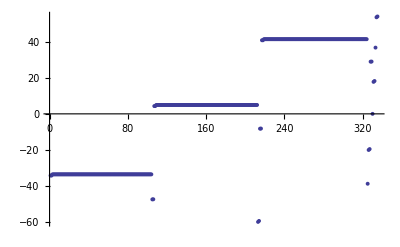

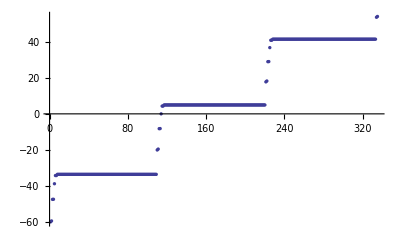

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.499,0.-160.499 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{15.928,Null}

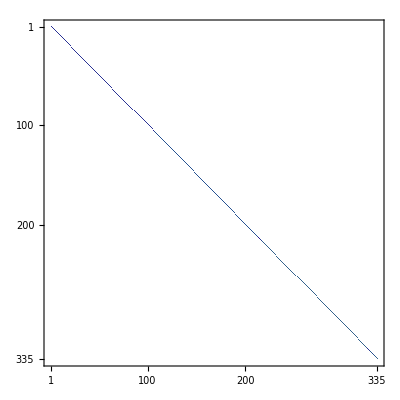

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

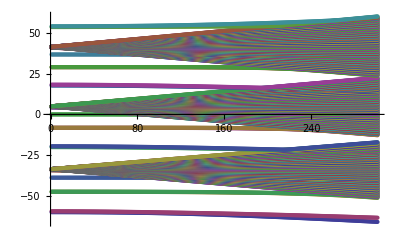

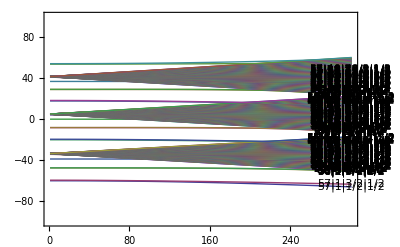

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

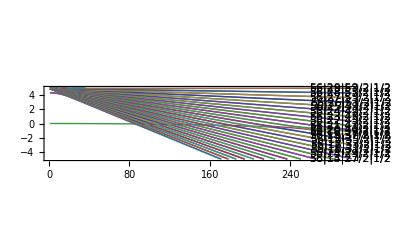

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-5,5}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

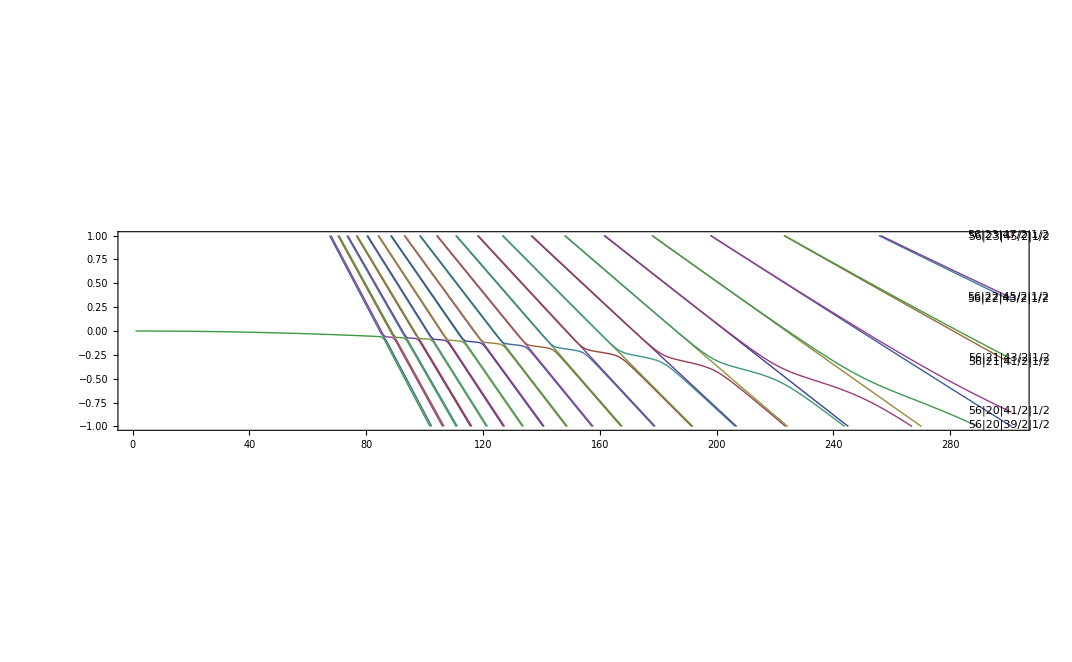

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[114]]
LabelList


MPList[[114]]

Export["59s_stark_Shift.dat",MPList[[114]]]
```

59|0|1/2|1/2

{57|1|1/2|1/2,57|1|3/2|1/2,56|2|3/2|1/2,56|2|5/2|1/2,58|0|1/2|1/2,55|3|7/2|1/2,55|3|5/2|1/2,55|4|7/2|1/2,55|4|9/2|1/2,55|5|9/2|1/2,55|5|11/2|1/2,55|6|11/2|1/2,55|6|13/2|1/2,55|7|13/2|1/2,55|7|15/2|1/2,55|8|15/2|1/2,55|8|17/2|1/2,55|9|17/2|1/2,55|9|19/2|1/2,55|10|19/2|1/2,55|10|21/2|1/2,55|11|21/2|1/2,55|11|23/2|1/2,55|12|23/2|1/2,55|12|25/2|1/2,55|13|25/2|1/2,55|13|27/2|1/2,55|14|27/2|1/2,55|14|29/2|1/2,55|15|29/2|1/2,55|15|31/2|1/2,55|16|31/2|1/2,55|16|33/2|1/2,55|17|33/2|1/2,55|17|35/2|1/2,55|18|35/2|1/2,55|18|37/2|1/2,55|19|37/2|1/2,55|19|39/2|1/2,55|20|39/2|1/2,55|20|41/2|1/2,55|21|41/2|1/2,55|21|43/2|1/2,55|22|43/2|1/2,55|22|45/2|1/2,55|23|45/2|1/2,55|23|47/2|1/2,55|24|47/2|1/2,55|24|49/2|1/2,55|25|49/2|1/2,55|25|51/2|1/2,55|26|51/2|1/2,55|26|53/2|1/2,55|27|53/2|1/2,55|27|55/2|1/2,55|28|55/2|1/2,55|28|57/2|1/2,55|29|57/2|1/2,55|29|59/2|1/2,55|30|59/2|1/2,55|30|61/2|1/2,55|31|61/2|1/2,55|31|63/2|1/2,55|32|63/2|1/2,55|32|65/2|1/2,55|33|65/2|1/2,55|33|67/2|1/2,55|34|67/2|1/2,55|34|69/2|1/2,55|35|69/2|1/2,55|35|71/2|1/2,55|36|71/2|1/2,55|36|73/2|1/2,55|37|73/2|1/2,55|37|75/2|1/2,55|38|75/2|1/2,55|38|77/2|1/2,55|39|77/2|1/2,55|39|79/2|1/2,55|40|79/2|1/2,55|40|81/2|1/2,55|41|81/2|1/2,55|41|83/2|1/2,55|42|83/2|1/2,55|42|85/2|1/2,55|43|85/2|1/2,55|43|87/2|1/2,55|44|87/2|1/2,55|44|89/2|1/2,55|45|89/2|1/2,55|45|91/2|1/2,55|46|91/2|1/2,55|46|93/2|1/2,55|47|93/2|1/2,55|47|95/2|1/2,55|48|95/2|1/2,55|48|97/2|1/2,55|49|97/2|1/2,55|49|99/2|1/2,55|50|99/2|1/2,55|50|101/2|1/2,55|51|101/2|1/2,55|51|103/2|1/2,55|52|103/2|1/2,55|52|105/2|1/2,55|53|105/2|1/2,55|53|107/2|1/2,55|54|107/2|1/2,55|54|109/2|1/2,58|1|1/2|1/2,58|1|3/2|1/2,57|2|3/2|1/2,57|2|5/2|1/2,59|0|1/2|1/2,56|3|7/2|1/2,56|3|5/2|1/2,56|4|7/2|1/2,56|4|9/2|1/2,56|5|9/2|1/2,56|5|11/2|1/2,56|6|11/2|1/2,56|6|13/2|1/2,56|7|13/2|1/2,56|7|15/2|1/2,56|8|15/2|1/2,56|8|17/2|1/2,56|9|17/2|1/2,56|9|19/2|1/2,56|10|19/2|1/2,56|10|21/2|1/2,56|11|21/2|1/2,56|11|23/2|1/2,56|12|23/2|1/2,56|12|25/2|1/2,56|13|25/2|1/2,56|13|27/2|1/2,56|14|27/2|1/2,56|14|29/2|1/2,56|15|29/2|1/2,56|15|31/2|1/2,56|16|31/2|1/2,56|16|33/2|1/2,56|17|33/2|1/2,56|17|35/2|1/2,56|18|35/2|1/2,56|18|37/2|1/2,56|19|37/2|1/2,56|19|39/2|1/2,56|20|39/2|1/2,56|20|41/2|1/2,56|21|41/2|1/2,56|21|43/2|1/2,56|22|43/2|1/2,56|22|45/2|1/2,56|23|45/2|1/2,56|23|47/2|1/2,56|24|47/2|1/2,56|24|49/2|1/2,56|25|49/2|1/2,56|25|51/2|1/2,56|26|51/2|1/2,56|26|53/2|1/2,56|27|53/2|1/2,56|27|55/2|1/2,56|28|55/2|1/2,56|28|57/2|1/2,56|29|57/2|1/2,56|29|59/2|1/2,56|30|59/2|1/2,56|30|61/2|1/2,56|31|61/2|1/2,56|31|63/2|1/2,56|32|63/2|1/2,56|32|65/2|1/2,56|33|65/2|1/2,56|33|67/2|1/2,56|34|67/2|1/2,56|34|69/2|1/2,56|35|69/2|1/2,56|35|71/2|1/2,56|36|71/2|1/2,56|36|73/2|1/2,56|37|73/2|1/2,56|37|75/2|1/2,56|38|75/2|1/2,56|38|77/2|1/2,56|39|77/2|1/2,56|39|79/2|1/2,56|40|79/2|1/2,56|40|81/2|1/2,56|41|81/2|1/2,56|41|83/2|1/2,56|42|83/2|1/2,56|42|85/2|1/2,56|43|85/2|1/2,56|43|87/2|1/2,56|44|87/2|1/2,56|44|89/2|1/2,56|45|89/2|1/2,56|45|91/2|1/2,56|46|91/2|1/2,56|46|93/2|1/2,56|47|93/2|1/2,56|47|95/2|1/2,56|48|95/2|1/2,56|48|97/2|1/2,56|49|97/2|1/2,56|49|99/2|1/2,56|50|99/2|1/2,56|50|101/2|1/2,56|51|101/2|1/2,56|51|103/2|1/2,56|52|103/2|1/2,56|52|105/2|1/2,56|53|105/2|1/2,56|53|107/2|1/2,56|54|107/2|1/2,56|54|109/2|1/2,56|55|109/2|1/2,56|55|111/2|1/2,59|1|1/2|1/2,59|1|3/2|1/2,58|2|3/2|1/2,58|2|5/2|1/2,60|0|1/2|1/2,57|3|7/2|1/2,57|3|5/2|1/2,57|4|7/2|1/2,57|4|9/2|1/2,57|5|9/2|1/2,57|5|11/2|1/2,57|6|11/2|1/2,57|6|13/2|1/2,57|7|13/2|1/2,57|7|15/2|1/2,57|8|15/2|1/2,57|8|17/2|1/2,57|9|17/2|1/2,57|9|19/2|1/2,57|10|19/2|1/2,57|10|21/2|1/2,57|11|21/2|1/2,57|11|23/2|1/2,57|12|23/2|1/2,57|12|25/2|1/2,57|13|25/2|1/2,57|13|27/2|1/2,57|14|27/2|1/2,57|14|29/2|1/2,57|15|29/2|1/2,57|15|31/2|1/2,57|16|31/2|1/2,57|16|33/2|1/2,57|17|33/2|1/2,57|17|35/2|1/2,57|18|35/2|1/2,57|18|37/2|1/2,57|19|37/2|1/2,57|19|39/2|1/2,57|20|39/2|1/2,57|20|41/2|1/2,57|21|41/2|1/2,57|21|43/2|1/2,57|22|43/2|1/2,57|22|45/2|1/2,57|23|45/2|1/2,57|23|47/2|1/2,57|24|47/2|1/2,57|24|49/2|1/2,57|25|49/2|1/2,57|25|51/2|1/2,57|26|51/2|1/2,57|26|53/2|1/2,57|27|53/2|1/2,57|27|55/2|1/2,57|28|55/2|1/2,57|28|57/2|1/2,57|29|57/2|1/2,57|29|59/2|1/2,57|30|59/2|1/2,57|30|61/2|1/2,57|31|61/2|1/2,57|31|63/2|1/2,57|32|63/2|1/2,57|32|65/2|1/2,57|33|65/2|1/2,57|33|67/2|1/2,57|34|67/2|1/2,57|34|69/2|1/2,57|35|69/2|1/2,57|35|71/2|1/2,57|36|71/2|1/2,57|36|73/2|1/2,57|37|73/2|1/2,57|37|75/2|1/2,57|38|75/2|1/2,57|38|77/2|1/2,57|39|77/2|1/2,57|39|79/2|1/2,57|40|79/2|1/2,57|40|81/2|1/2,57|41|81/2|1/2,57|41|83/2|1/2,57|42|83/2|1/2,57|42|85/2|1/2,57|43|85/2|1/2,57|43|87/2|1/2,57|44|87/2|1/2,57|44|89/2|1/2,57|45|89/2|1/2,57|45|91/2|1/2,57|46|91/2|1/2,57|46|93/2|1/2,57|47|93/2|1/2,57|47|95/2|1/2,57|48|95/2|1/2,57|48|97/2|1/2,57|49|97/2|1/2,57|49|99/2|1/2,57|50|99/2|1/2,57|50|101/2|1/2,57|51|101/2|1/2,57|51|103/2|1/2,57|52|103/2|1/2,57|52|105/2|1/2,57|53|105/2|1/2,57|53|107/2|1/2,57|54|107/2|1/2,57|54|109/2|1/2,57|55|109/2|1/2,57|55|111/2|1/2,57|56|111/2|1/2,57|56|113/2|1/2,60|1|1/2|1/2,60|1|3/2|1/2}

{{1,-7.98532×10^-6},{2,-0.0000319415},{3,-0.000071869},{4,-0.000127769},{5,-0.000199642},{6,-0.000287491},{7,-0.000391317},{8,-0.000511122},{9,-0.000646911},{10,-0.000798685},{11,-0.000966448},{12,-0.0011502},{13,-0.00134996},{14,-0.00156572},{15,-0.00179748},{16,-0.00204526},{17,-0.00230905},{18,-0.00258888},{19,-0.00288473},{20,-0.00319663},{21,-0.00352457},{22,-0.00386857},{23,-0.00422864},{24,-0.00460478},{25,-0.00499701},{26,-0.00540533},{27,-0.00582976},{28,-0.0062703},{29,-0.00672698},{30,-0.0071998},{31,-0.00768877},{32,-0.00819392},{33,-0.00871525},{34,-0.00925279},{35,-0.00980654},{36,-0.0103765},{37,-0.0109628},{38,-0.0115653},{39,-0.0121841},{40,-0.0128192},{41,-0.0134706},{42,-0.0141384},{43,-0.0148226},{44,-0.0155232},{45,-0.0162402},{46,-0.0169737},{47,-0.0177236},{48,-0.0184901},{49,-0.0192731},{50,-0.0200726},{51,-0.0208888},{52,-0.0217217},{53,-0.0225712},{54,-0.0234374},{55,-0.0243204},{56,-0.0252202},{57,-0.0261369},{58,-0.0270704},{59,-0.0280209},{60,-0.0289884},{61,-0.0299729},{62,-0.0309746},{63,-0.0319935},{64,-0.0330296},{65,-0.034083},{66,-0.0351538},{67,-0.0362421},{68,-0.037348},{69,-0.0384716},{70,-0.0396129},{71,-0.0407722},{72,-0.0419495},{73,-0.043145},{74,-0.0443589},{75,-0.0455915},{76,-0.0468429},{77,-0.0481135},{78,-0.0494037},{79,-0.0507141},{80,-0.0520456},{81,-0.0533995},{82,-0.0547782},{83,-0.0561872},{84,-0.057643},{85,-0.0592505},{86,-0.079279},{87,-0.13704},{88,-0.195178},{89,-0.253353},{90,-0.31154},{91,-0.369732},{92,-0.427926},{93,-0.486122},{94,-0.544319},{95,-0.602516},{96,-0.660713},{97,-0.71891},{98,-0.777107},{99,-0.835304},{100,-0.8935},{101,-0.951696},{102,-1.00989},{103,-1.06809},{104,-1.12628},{105,-1.18447},{106,-1.24267},{107,-1.30086},{108,-1.35905},{109,-1.41724},{110,-1.47543},{111,-1.53362},{112,-1.5918},{113,-1.64999},{114,-1.70817},{115,-1.76635},{116,-1.82454},{117,-1.88272},{118,-1.94089},{119,-1.99907},{120,-2.05725},{121,-2.11542},{122,-2.17359},{123,-2.23176},{124,-2.28993},{125,-2.34809},{126,-2.40626},{127,-2.46442},{128,-2.52257},{129,-2.58073},{130,-2.63888},{131,-2.69704},{132,-2.75518},{133,-2.81333},{134,-2.87147},{135,-2.92961},{136,-2.98775},{137,-3.04588},{138,-3.10401},{139,-3.16213},{140,-3.22026},{141,-3.27837},{142,-3.33649},{143,-3.3946},{144,-3.4527},{145,-3.51081},{146,-3.5689},{147,-3.627},{148,-3.68508},{149,-3.74316},{150,-3.80124},{151,-3.85931},{152,-3.91738},{153,-3.97544},{154,-4.03349},{155,-4.09154},{156,-4.14958},{157,-4.20761},{158,-4.26564},{159,-4.32366},{160,-4.38167},{161,-4.43967},{162,-4.49767},{163,-4.55566},{164,-4.61364},{165,-4.67161},{166,-4.72956},{167,-4.78751},{168,-4.84545},{169,-4.90338},{170,-4.9613},{171,-5.01921},{172,-5.0771},{173,-5.13498},{174,-5.19285},{175,-5.25071},{176,-5.30855},{177,-5.36638},{178,-5.42419},{179,-5.48199},{180,-5.53977},{181,-5.59753},{182,-5.65528},{183,-5.713},{184,-5.77071},{185,-5.8284},{186,-5.88607},{187,-5.94371},{188,-6.00133},{189,-6.05893},{190,-6.1165},{191,-6.17405},{192,-6.23157},{193,-6.28906},{194,-6.34652},{195,-6.40395},{196,-6.46135},{197,-6.51871},{198,-6.57604},{199,-6.63333},{200,-6.69058},{201,-6.74779},{202,-6.80496},{203,-6.86208},{204,-6.91916},{205,-6.97618},{206,-7.03315},{207,-7.09007},{208,-7.14693},{209,-7.20372},{210,-7.26046},{211,-7.31712},{212,-7.37372},{213,-7.43023},{214,-7.48668},{215,-7.54303},{216,-7.5993},{217,-7.65548},{218,-7.71157},{219,-7.76755},{220,-7.82342},{221,-7.87918},{222,-7.93483},{223,-7.99035},{224,-8.04574},{225,-8.10099},{226,-8.1561},{227,-8.21106},{228,-8.26587},{229,-8.32051},{230,-8.37498},{231,-8.42928},{232,-8.4834},{233,-8.53733},{234,-8.59107},{235,-8.64461},{236,-8.69795},{237,-8.75109},{238,-8.80401},{239,-8.85673},{240,-8.90924},{241,-8.96154},{242,-9.01362},{243,-9.0655},{244,-9.11718},{245,-9.16865},{246,-9.21994},{247,-9.27103},{248,-9.32195},{249,-9.37271},{250,-9.42333},{251,-9.47381},{252,-9.52417},{253,-9.57444},{254,-9.62464},{255,-9.67478},{256,-9.72489},{257,-9.77499},{258,-9.8251},{259,-9.87523},{260,-9.92541},{261,-9.97565},{262,-10.026},{263,-10.0764},{264,-10.1269},{265,-10.1775},{266,-10.2282},{267,-10.279},{268,-10.33},{269,-10.3811},{270,-10.4324},{271,-10.4837},{272,-10.5353},{273,-10.5869},{274,-10.6387},{275,-10.6906},{276,-10.7427},{277,-10.7949},{278,-10.8472},{279,-10.8997},{280,-10.9522},{281,-11.0049},{282,-11.0577},{283,-11.1106},{284,-11.1637},{285,-11.2168},{286,-11.27},{287,-11.3234},{288,-11.3768},{289,-11.4303},{290,-11.4839},{291,-11.5376},{292,-11.5914},{293,-11.6452},{294,-11.6992},{295,-11.7532},{296,-11.8072},{297,-11.8614},{298,-11.9156},{299,-11.9699},{300,-12.0242},{301,-12.0786}}

59s_stark_Shift.dat

## | 60 s1/2 >, | 59 p1/2 >, | 59 p3/2 >, | 60 p1/2 >, | 60 p3/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

δf=200*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-1.01724×10^12

{0.592,Null}

1363

{{52,4,7/2,1/2,-1.21665×10^12,1},{52,4,9/2,1/2,-1.21665×10^12,1},{52,5,9/2,1/2,-1.21665×10^12,-1},{52,5,11/2,1/2,-1.21665×10^12,-1},{52,6,11/2,1/2,-1.21665×10^12,1},{52,6,13/2,1/2,-1.21665×10^12,1},{52,7,13/2,1/2,-1.21665×10^12,-1},{52,7,15/2,1/2,-1.21665×10^12,-1},{52,8,15/2,1/2,-1.21665×10^12,1},{52,8,17/2,1/2,-1.21665×10^12,1},{52,9,17/2,1/2,-1.21665×10^12,-1},«1341»,{64,0,1/2,1/2,-8.87939×10^11,1},{64,1,1/2,1/2,-8.74205×10^11,-1},{64,1,3/2,1/2,-8.73829×10^11,-1},{64,2,3/2,1/2,-8.38111×10^11,1},{64,2,5/2,1/2,-8.38068×10^11,1},{65,0,1/2,1/2,-8.59467×10^11,1},{65,1,1/2,1/2,-8.46386×10^11,-1},{65,1,3/2,1/2,-8.46027×10^11,-1},{66,0,1/2,1/2,-8.32343×10^11,1},{66,1,1/2,1/2,-8.19874×10^11,-1},{66,1,3/2,1/2,-8.19532×10^11,-1}}

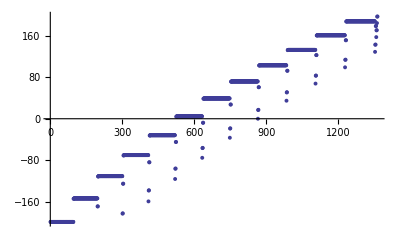

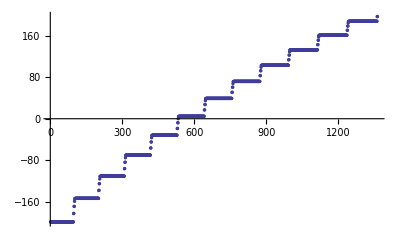

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);


EMatrixelement[{60,0,1/2,1/2},{63,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{62,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{61,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{60,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{59,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{57,1,1/2,-1/2}]
EMatrixelement[{60,0,1/2,1/2},{56,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

{52|4|7/2|1/2,52|4|9/2|1/2,52|5|9/2|1/2,52|5|11/2|1/2,52|6|11/2|1/2,52|6|13/2|1/2,52|7|13/2|1/2,52|7|15/2|1/2,52|8|15/2|1/2,52|8|17/2|1/2,52|9|17/2|1/2,52|9|19/2|1/2,52|10|19/2|1/2,52|10|21/2|1/2,52|11|21/2|1/2,52|11|23/2|1/2,52|12|23/2|1/2,52|12|25/2|1/2,52|13|25/2|1/2,52|13|27/2|1/2,52|14|27/2|1/2,52|14|29/2|1/2,52|15|29/2|1/2,52|15|31/2|1/2,52|16|31/2|1/2,52|16|33/2|1/2,52|17|33/2|1/2,52|17|35/2|1/2,52|18|35/2|1/2,52|18|37/2|1/2,52|19|37/2|1/2,52|19|39/2|1/2,52|20|39/2|1/2,52|20|41/2|1/2,52|21|41/2|1/2,52|21|43/2|1/2,52|22|43/2|1/2,52|22|45/2|1/2,52|23|45/2|1/2,52|23|47/2|1/2,52|24|47/2|1/2,52|24|49/2|1/2,52|25|49/2|1/2,52|25|51/2|1/2,52|26|51/2|1/2,52|26|53/2|1/2,52|27|53/2|1/2,52|27|55/2|1/2,52|28|55/2|1/2,52|28|57/2|1/2,52|29|57/2|1/2,52|29|59/2|1/2,52|30|59/2|1/2,52|30|61/2|1/2,52|31|61/2|1/2,52|31|63/2|1/2,52|32|63/2|1/2,52|32|65/2|1/2,52|33|65/2|1/2,52|33|67/2|1/2,52|34|67/2|1/2,52|34|69/2|1/2,52|35|69/2|1/2,52|35|71/2|1/2,52|36|71/2|1/2,52|36|73/2|1/2,52|37|73/2|1/2,52|37|75/2|1/2,52|38|75/2|1/2,52|38|77/2|1/2,52|39|77/2|1/2,52|39|79/2|1/2,52|40|79/2|1/2,52|40|81/2|1/2,52|41|81/2|1/2,52|41|83/2|1/2,52|42|83/2|1/2,52|42|85/2|1/2,52|43|85/2|1/2,52|43|87/2|1/2,52|44|87/2|1/2,52|44|89/2|1/2,52|45|89/2|1/2,52|45|91/2|1/2,52|46|91/2|1/2,52|46|93/2|1/2,52|47|93/2|1/2,52|47|95/2|1/2,52|48|95/2|1/2,52|48|97/2|1/2,52|49|97/2|1/2,52|49|99/2|1/2,52|50|99/2|1/2,52|50|101/2|1/2,52|51|101/2|1/2,52|51|103/2|1/2,55|1|1/2|1/2,55|1|3/2|1/2,54|2|3/2|1/2,54|2|5/2|1/2,56|0|1/2|1/2,53|3|7/2|1/2,53|3|5/2|1/2,53|4|7/2|1/2,53|4|9/2|1/2,53|5|9/2|1/2,53|5|11/2|1/2,53|6|11/2|1/2,53|6|13/2|1/2,53|7|13/2|1/2,53|7|15/2|1/2,53|8|15/2|1/2,53|8|17/2|1/2,53|9|17/2|1/2,53|9|19/2|1/2,53|10|19/2|1/2,53|10|21/2|1/2,53|11|21/2|1/2,53|11|23/2|1/2,53|12|23/2|1/2,53|12|25/2|1/2,53|13|25/2|1/2,53|13|27/2|1/2,53|14|27/2|1/2,53|14|29/2|1/2,53|15|29/2|1/2,53|15|31/2|1/2,53|16|31/2|1/2,53|16|33/2|1/2,53|17|33/2|1/2,53|17|35/2|1/2,53|18|35/2|1/2,53|18|37/2|1/2,53|19|37/2|1/2,53|19|39/2|1/2,53|20|39/2|1/2,53|20|41/2|1/2,53|21|41/2|1/2,53|21|43/2|1/2,53|22|43/2|1/2,53|22|45/2|1/2,53|23|45/2|1/2,53|23|47/2|1/2,53|24|47/2|1/2,53|24|49/2|1/2,53|25|49/2|1/2,53|25|51/2|1/2,53|26|51/2|1/2,53|26|53/2|1/2,53|27|53/2|1/2,53|27|55/2|1/2,53|28|55/2|1/2,53|28|57/2|1/2,53|29|57/2|1/2,53|29|59/2|1/2,53|30|59/2|1/2,53|30|61/2|1/2,53|31|61/2|1/2,53|31|63/2|1/2,53|32|63/2|1/2,53|32|65/2|1/2,53|33|65/2|1/2,53|33|67/2|1/2,53|34|67/2|1/2,53|34|69/2|1/2,53|35|69/2|1/2,53|35|71/2|1/2,53|36|71/2|1/2,53|36|73/2|1/2,53|37|73/2|1/2,53|37|75/2|1/2,53|38|75/2|1/2,53|38|77/2|1/2,53|39|77/2|1/2,53|39|79/2|1/2,53|40|79/2|1/2,53|40|81/2|1/2,53|41|81/2|1/2,53|41|83/2|1/2,53|42|83/2|1/2,53|42|85/2|1/2,53|43|85/2|1/2,53|43|87/2|1/2,53|44|87/2|1/2,53|44|89/2|1/2,53|45|89/2|1/2,53|45|91/2|1/2,53|46|91/2|1/2,53|46|93/2|1/2,53|47|93/2|1/2,53|47|95/2|1/2,53|48|95/2|1/2,53|48|97/2|1/2,53|49|97/2|1/2,53|49|99/2|1/2,53|50|99/2|1/2,53|50|101/2|1/2,53|51|101/2|1/2,53|51|103/2|1/2,53|52|103/2|1/2,53|52|105/2|1/2,56|1|1/2|1/2,56|1|3/2|1/2,55|2|3/2|1/2,55|2|5/2|1/2,57|0|1/2|1/2,54|3|7/2|1/2,54|3|5/2|1/2,54|4|7/2|1/2,54|4|9/2|1/2,54|5|9/2|1/2,54|5|11/2|1/2,54|6|11/2|1/2,54|6|13/2|1/2,54|7|13/2|1/2,54|7|15/2|1/2,54|8|15/2|1/2,54|8|17/2|1/2,54|9|17/2|1/2,54|9|19/2|1/2,54|10|19/2|1/2,54|10|21/2|1/2,54|11|21/2|1/2,54|11|23/2|1/2,54|12|23/2|1/2,54|12|25/2|1/2,54|13|25/2|1/2,54|13|27/2|1/2,54|14|27/2|1/2,54|14|29/2|1/2,54|15|29/2|1/2,54|15|31/2|1/2,54|16|31/2|1/2,54|16|33/2|1/2,54|17|33/2|1/2,54|17|35/2|1/2,54|18|35/2|1/2,54|18|37/2|1/2,54|19|37/2|1/2,54|19|39/2|1/2,54|20|39/2|1/2,54|20|41/2|1/2,54|21|41/2|1/2,54|21|43/2|1/2,54|22|43/2|1/2,54|22|45/2|1/2,54|23|45/2|1/2,54|23|47/2|1/2,54|24|47/2|1/2,54|24|49/2|1/2,54|25|49/2|1/2,54|25|51/2|1/2,54|26|51/2|1/2,54|26|53/2|1/2,54|27|53/2|1/2,54|27|55/2|1/2,54|28|55/2|1/2,54|28|57/2|1/2,54|29|57/2|1/2,54|29|59/2|1/2,54|30|59/2|1/2,54|30|61/2|1/2,54|31|61/2|1/2,54|31|63/2|1/2,54|32|63/2|1/2,54|32|65/2|1/2,54|33|65/2|1/2,54|33|67/2|1/2,54|34|67/2|1/2,54|34|69/2|1/2,54|35|69/2|1/2,54|35|71/2|1/2,54|36|71/2|1/2,54|36|73/2|1/2,54|37|73/2|1/2,54|37|75/2|1/2,54|38|75/2|1/2,54|38|77/2|1/2,54|39|77/2|1/2,54|39|79/2|1/2,54|40|79/2|1/2,54|40|81/2|1/2,54|41|81/2|1/2,54|41|83/2|1/2,54|42|83/2|1/2,54|42|85/2|1/2,54|43|85/2|1/2,54|43|87/2|1/2,54|44|87/2|1/2,54|44|89/2|1/2,54|45|89/2|1/2,54|45|91/2|1/2,54|46|91/2|1/2,54|46|93/2|1/2,54|47|93/2|1/2,54|47|95/2|1/2,54|48|95/2|1/2,54|48|97/2|1/2,54|49|97/2|1/2,54|49|99/2|1/2,54|50|99/2|1/2,54|50|101/2|1/2,54|51|101/2|1/2,54|51|103/2|1/2,54|52|103/2|1/2,54|52|105/2|1/2,54|53|105/2|1/2,54|53|107/2|1/2,57|1|1/2|1/2,57|1|3/2|1/2,56|2|3/2|1/2,56|2|5/2|1/2,58|0|1/2|1/2,55|3|7/2|1/2,55|3|5/2|1/2,55|4|7/2|1/2,55|4|9/2|1/2,55|5|9/2|1/2,55|5|11/2|1/2,55|6|11/2|1/2,55|6|13/2|1/2,55|7|13/2|1/2,55|7|15/2|1/2,55|8|15/2|1/2,55|8|17/2|1/2,55|9|17/2|1/2,55|9|19/2|1/2,55|10|19/2|1/2,55|10|21/2|1/2,55|11|21/2|1/2,55|11|23/2|1/2,55|12|23/2|1/2,55|12|25/2|1/2,55|13|25/2|1/2,55|13|27/2|1/2,55|14|27/2|1/2,55|14|29/2|1/2,55|15|29/2|1/2,55|15|31/2|1/2,55|16|31/2|1/2,55|16|33/2|1/2,55|17|33/2|1/2,55|17|35/2|1/2,55|18|35/2|1/2,55|18|37/2|1/2,55|19|37/2|1/2,55|19|39/2|1/2,55|20|39/2|1/2,55|20|41/2|1/2,55|21|41/2|1/2,55|21|43/2|1/2,55|22|43/2|1/2,55|22|45/2|1/2,55|23|45/2|1/2,55|23|47/2|1/2,55|24|47/2|1/2,55|24|49/2|1/2,55|25|49/2|1/2,55|25|51/2|1/2,55|26|51/2|1/2,55|26|53/2|1/2,55|27|53/2|1/2,55|27|55/2|1/2,55|28|55/2|1/2,55|28|57/2|1/2,55|29|57/2|1/2,55|29|59/2|1/2,55|30|59/2|1/2,55|30|61/2|1/2,55|31|61/2|1/2,55|31|63/2|1/2,55|32|63/2|1/2,55|32|65/2|1/2,55|33|65/2|1/2,55|33|67/2|1/2,55|34|67/2|1/2,55|34|69/2|1/2,55|35|69/2|1/2,55|35|71/2|1/2,55|36|71/2|1/2,55|36|73/2|1/2,55|37|73/2|1/2,55|37|75/2|1/2,55|38|75/2|1/2,55|38|77/2|1/2,55|39|77/2|1/2,55|39|79/2|1/2,55|40|79/2|1/2,55|40|81/2|1/2,55|41|81/2|1/2,55|41|83/2|1/2,55|42|83/2|1/2,55|42|85/2|1/2,55|43|85/2|1/2,55|43|87/2|1/2,55|44|87/2|1/2,55|44|89/2|1/2,55|45|89/2|1/2,55|45|91/2|1/2,55|46|91/2|1/2,55|46|93/2|1/2,55|47|93/2|1/2,55|47|95/2|1/2,55|48|95/2|1/2,55|48|97/2|1/2,55|49|97/2|1/2,55|49|99/2|1/2,55|50|99/2|1/2,55|50|101/2|1/2,55|51|101/2|1/2,55|51|103/2|1/2,55|52|103/2|1/2,55|52|105/2|1/2,55|53|105/2|1/2,55|53|107/2|1/2,55|54|107/2|1/2,55|54|109/2|1/2,58|1|1/2|1/2,58|1|3/2|1/2,57|2|3/2|1/2,57|2|5/2|1/2,59|0|1/2|1/2,56|3|7/2|1/2,56|3|5/2|1/2,56|4|7/2|1/2,56|4|9/2|1/2,56|5|9/2|1/2,56|5|11/2|1/2,56|6|11/2|1/2,56|6|13/2|1/2,56|7|13/2|1/2,56|7|15/2|1/2,56|8|15/2|1/2,56|8|17/2|1/2,56|9|17/2|1/2,56|9|19/2|1/2,56|10|19/2|1/2,56|10|21/2|1/2,56|11|21/2|1/2,56|11|23/2|1/2,56|12|23/2|1/2,56|12|25/2|1/2,56|13|25/2|1/2,56|13|27/2|1/2,56|14|27/2|1/2,56|14|29/2|1/2,56|15|29/2|1/2,56|15|31/2|1/2,56|16|31/2|1/2,56|16|33/2|1/2,56|17|33/2|1/2,56|17|35/2|1/2,56|18|35/2|1/2,56|18|37/2|1/2,56|19|37/2|1/2,56|19|39/2|1/2,56|20|39/2|1/2,56|20|41/2|1/2,56|21|41/2|1/2,56|21|43/2|1/2,56|22|43/2|1/2,56|22|45/2|1/2,56|23|45/2|1/2,56|23|47/2|1/2,56|24|47/2|1/2,56|24|49/2|1/2,56|25|49/2|1/2,56|25|51/2|1/2,56|26|51/2|1/2,56|26|53/2|1/2,56|27|53/2|1/2,56|27|55/2|1/2,56|28|55/2|1/2,56|28|57/2|1/2,56|29|57/2|1/2,56|29|59/2|1/2,56|30|59/2|1/2,56|30|61/2|1/2,56|31|61/2|1/2,56|31|63/2|1/2,56|32|63/2|1/2,56|32|65/2|1/2,56|33|65/2|1/2,56|33|67/2|1/2,56|34|67/2|1/2,56|34|69/2|1/2,56|35|69/2|1/2,56|35|71/2|1/2,56|36|71/2|1/2,56|36|73/2|1/2,56|37|73/2|1/2,56|37|75/2|1/2,56|38|75/2|1/2,56|38|77/2|1/2,56|39|77/2|1/2,56|39|79/2|1/2,56|40|79/2|1/2,56|40|81/2|1/2,56|41|81/2|1/2,56|41|83/2|1/2,56|42|83/2|1/2,56|42|85/2|1/2,56|43|85/2|1/2,56|43|87/2|1/2,56|44|87/2|1/2,56|44|89/2|1/2,56|45|89/2|1/2,56|45|91/2|1/2,56|46|91/2|1/2,56|46|93/2|1/2,56|47|93/2|1/2,56|47|95/2|1/2,56|48|95/2|1/2,56|48|97/2|1/2,56|49|97/2|1/2,56|49|99/2|1/2,56|50|99/2|1/2,56|50|101/2|1/2,56|51|101/2|1/2,56|51|103/2|1/2,56|52|103/2|1/2,56|52|105/2|1/2,56|53|105/2|1/2,56|53|107/2|1/2,56|54|107/2|1/2,56|54|109/2|1/2,56|55|109/2|1/2,56|55|111/2|1/2,59|1|1/2|1/2,59|1|3/2|1/2,58|2|3/2|1/2,58|2|5/2|1/2,60|0|1/2|1/2,57|3|7/2|1/2,57|3|5/2|1/2,57|4|7/2|1/2,57|4|9/2|1/2,57|5|9/2|1/2,57|5|11/2|1/2,57|6|11/2|1/2,57|6|13/2|1/2,57|7|13/2|1/2,57|7|15/2|1/2,57|8|15/2|1/2,57|8|17/2|1/2,57|9|17/2|1/2,57|9|19/2|1/2,57|10|19/2|1/2,57|10|21/2|1/2,57|11|21/2|1/2,57|11|23/2|1/2,57|12|23/2|1/2,57|12|25/2|1/2,57|13|25/2|1/2,57|13|27/2|1/2,57|14|27/2|1/2,57|14|29/2|1/2,57|15|29/2|1/2,57|15|31/2|1/2,57|16|31/2|1/2,57|16|33/2|1/2,57|17|33/2|1/2,57|17|35/2|1/2,57|18|35/2|1/2,57|18|37/2|1/2,57|19|37/2|1/2,57|19|39/2|1/2,57|20|39/2|1/2,57|20|41/2|1/2,57|21|41/2|1/2,57|21|43/2|1/2,57|22|43/2|1/2,57|22|45/2|1/2,57|23|45/2|1/2,57|23|47/2|1/2,57|24|47/2|1/2,57|24|49/2|1/2,57|25|49/2|1/2,57|25|51/2|1/2,57|26|51/2|1/2,57|26|53/2|1/2,57|27|53/2|1/2,57|27|55/2|1/2,57|28|55/2|1/2,57|28|57/2|1/2,57|29|57/2|1/2,57|29|59/2|1/2,57|30|59/2|1/2,57|30|61/2|1/2,57|31|61/2|1/2,57|31|63/2|1/2,57|32|63/2|1/2,57|32|65/2|1/2,57|33|65/2|1/2,57|33|67/2|1/2,57|34|67/2|1/2,57|34|69/2|1/2,57|35|69/2|1/2,57|35|71/2|1/2,57|36|71/2|1/2,57|36|73/2|1/2,57|37|73/2|1/2,57|37|75/2|1/2,57|38|75/2|1/2,57|38|77/2|1/2,57|39|77/2|1/2,57|39|79/2|1/2,57|40|79/2|1/2,57|40|81/2|1/2,57|41|81/2|1/2,57|41|83/2|1/2,57|42|83/2|1/2,57|42|85/2|1/2,57|43|85/2|1/2,57|43|87/2|1/2,57|44|87/2|1/2,57|44|89/2|1/2,57|45|89/2|1/2,57|45|91/2|1/2,57|46|91/2|1/2,57|46|93/2|1/2,57|47|93/2|1/2,57|47|95/2|1/2,57|48|95/2|1/2,57|48|97/2|1/2,57|49|97/2|1/2,57|49|99/2|1/2,57|50|99/2|1/2,57|50|101/2|1/2,57|51|101/2|1/2,57|51|103/2|1/2,57|52|103/2|1/2,57|52|105/2|1/2,57|53|105/2|1/2,57|53|107/2|1/2,57|54|107/2|1/2,57|54|109/2|1/2,57|55|109/2|1/2,57|55|111/2|1/2,57|56|111/2|1/2,57|56|113/2|1/2,60|1|1/2|1/2,60|1|3/2|1/2,59|2|3/2|1/2,59|2|5/2|1/2,61|0|1/2|1/2,58|3|7/2|1/2,58|3|5/2|1/2,58|4|7/2|1/2,58|4|9/2|1/2,58|5|9/2|1/2,58|5|11/2|1/2,58|6|11/2|1/2,58|6|13/2|1/2,58|7|13/2|1/2,58|7|15/2|1/2,58|8|15/2|1/2,58|8|17/2|1/2,58|9|17/2|1/2,58|9|19/2|1/2,58|10|19/2|1/2,58|10|21/2|1/2,58|11|21/2|1/2,58|11|23/2|1/2,58|12|23/2|1/2,58|12|25/2|1/2,58|13|25/2|1/2,58|13|27/2|1/2,58|14|27/2|1/2,58|14|29/2|1/2,58|15|29/2|1/2,58|15|31/2|1/2,58|16|31/2|1/2,58|16|33/2|1/2,58|17|33/2|1/2,58|17|35/2|1/2,58|18|35/2|1/2,58|18|37/2|1/2,58|19|37/2|1/2,58|19|39/2|1/2,58|20|39/2|1/2,58|20|41/2|1/2,58|21|41/2|1/2,58|21|43/2|1/2,58|22|43/2|1/2,58|22|45/2|1/2,58|23|45/2|1/2,58|23|47/2|1/2,58|24|47/2|1/2,58|24|49/2|1/2,58|25|49/2|1/2,58|25|51/2|1/2,58|26|51/2|1/2,58|26|53/2|1/2,58|27|53/2|1/2,58|27|55/2|1/2,58|28|55/2|1/2,58|28|57/2|1/2,58|29|57/2|1/2,58|29|59/2|1/2,58|30|59/2|1/2,58|30|61/2|1/2,58|31|61/2|1/2,58|31|63/2|1/2,58|32|63/2|1/2,58|32|65/2|1/2,58|33|65/2|1/2,58|33|67/2|1/2,58|34|67/2|1/2,58|34|69/2|1/2,58|35|69/2|1/2,58|35|71/2|1/2,58|36|71/2|1/2,58|36|73/2|1/2,58|37|73/2|1/2,58|37|75/2|1/2,58|38|75/2|1/2,58|38|77/2|1/2,58|39|77/2|1/2,58|39|79/2|1/2,58|40|79/2|1/2,58|40|81/2|1/2,58|41|81/2|1/2,58|41|83/2|1/2,58|42|83/2|1/2,58|42|85/2|1/2,58|43|85/2|1/2,58|43|87/2|1/2,58|44|87/2|1/2,58|44|89/2|1/2,58|45|89/2|1/2,58|45|91/2|1/2,58|46|91/2|1/2,58|46|93/2|1/2,58|47|93/2|1/2,58|47|95/2|1/2,58|48|95/2|1/2,58|48|97/2|1/2,58|49|97/2|1/2,58|49|99/2|1/2,58|50|99/2|1/2,58|50|101/2|1/2,58|51|101/2|1/2,58|51|103/2|1/2,58|52|103/2|1/2,58|52|105/2|1/2,58|53|105/2|1/2,58|53|107/2|1/2,58|54|107/2|1/2,58|54|109/2|1/2,58|55|109/2|1/2,58|55|111/2|1/2,58|56|111/2|1/2,58|56|113/2|1/2,58|57|113/2|1/2,58|57|115/2|1/2,61|1|1/2|1/2,61|1|3/2|1/2,60|2|3/2|1/2,60|2|5/2|1/2,62|0|1/2|1/2,59|3|7/2|1/2,59|3|5/2|1/2,59|4|7/2|1/2,59|4|9/2|1/2,59|5|9/2|1/2,59|5|11/2|1/2,59|6|11/2|1/2,59|6|13/2|1/2,59|7|13/2|1/2,59|7|15/2|1/2,59|8|15/2|1/2,59|8|17/2|1/2,59|9|17/2|1/2,59|9|19/2|1/2,59|10|19/2|1/2,59|10|21/2|1/2,59|11|21/2|1/2,59|11|23/2|1/2,59|12|23/2|1/2,59|12|25/2|1/2,59|13|25/2|1/2,59|13|27/2|1/2,59|14|27/2|1/2,59|14|29/2|1/2,59|15|29/2|1/2,59|15|31/2|1/2,59|16|31/2|1/2,59|16|33/2|1/2,59|17|33/2|1/2,59|17|35/2|1/2,59|18|35/2|1/2,59|18|37/2|1/2,59|19|37/2|1/2,59|19|39/2|1/2,59|20|39/2|1/2,59|20|41/2|1/2,59|21|41/2|1/2,59|21|43/2|1/2,59|22|43/2|1/2,59|22|45/2|1/2,59|23|45/2|1/2,59|23|47/2|1/2,59|24|47/2|1/2,59|24|49/2|1/2,59|25|49/2|1/2,59|25|51/2|1/2,59|26|51/2|1/2,59|26|53/2|1/2,59|27|53/2|1/2,59|27|55/2|1/2,59|28|55/2|1/2,59|28|57/2|1/2,59|29|57/2|1/2,59|29|59/2|1/2,59|30|59/2|1/2,59|30|61/2|1/2,59|31|61/2|1/2,59|31|63/2|1/2,59|32|63/2|1/2,59|32|65/2|1/2,59|33|65/2|1/2,59|33|67/2|1/2,59|34|67/2|1/2,59|34|69/2|1/2,59|35|69/2|1/2,59|35|71/2|1/2,59|36|71/2|1/2,59|36|73/2|1/2,59|37|73/2|1/2,59|37|75/2|1/2,59|38|75/2|1/2,59|38|77/2|1/2,59|39|77/2|1/2,59|39|79/2|1/2,59|40|79/2|1/2,59|40|81/2|1/2,59|41|81/2|1/2,59|41|83/2|1/2,59|42|83/2|1/2,59|42|85/2|1/2,59|43|85/2|1/2,59|43|87/2|1/2,59|44|87/2|1/2,59|44|89/2|1/2,59|45|89/2|1/2,59|45|91/2|1/2,59|46|91/2|1/2,59|46|93/2|1/2,59|47|93/2|1/2,59|47|95/2|1/2,59|48|95/2|1/2,59|48|97/2|1/2,59|49|97/2|1/2,59|49|99/2|1/2,59|50|99/2|1/2,59|50|101/2|1/2,59|51|101/2|1/2,59|51|103/2|1/2,59|52|103/2|1/2,59|52|105/2|1/2,59|53|105/2|1/2,59|53|107/2|1/2,59|54|107/2|1/2,59|54|109/2|1/2,59|55|109/2|1/2,59|55|111/2|1/2,59|56|111/2|1/2,59|56|113/2|1/2,59|57|113/2|1/2,59|57|115/2|1/2,59|58|115/2|1/2,59|58|117/2|1/2,62|1|1/2|1/2,62|1|3/2|1/2,61|2|3/2|1/2,61|2|5/2|1/2,63|0|1/2|1/2,60|3|7/2|1/2,60|3|5/2|1/2,60|4|7/2|1/2,60|4|9/2|1/2,60|5|9/2|1/2,60|5|11/2|1/2,60|6|11/2|1/2,60|6|13/2|1/2,60|7|13/2|1/2,60|7|15/2|1/2,60|8|15/2|1/2,60|8|17/2|1/2,60|9|17/2|1/2,60|9|19/2|1/2,60|10|19/2|1/2,60|10|21/2|1/2,60|11|21/2|1/2,60|11|23/2|1/2,60|12|23/2|1/2,60|12|25/2|1/2,60|13|25/2|1/2,60|13|27/2|1/2,60|14|27/2|1/2,60|14|29/2|1/2,60|15|29/2|1/2,60|15|31/2|1/2,60|16|31/2|1/2,60|16|33/2|1/2,60|17|33/2|1/2,60|17|35/2|1/2,60|18|35/2|1/2,60|18|37/2|1/2,60|19|37/2|1/2,60|19|39/2|1/2,60|20|39/2|1/2,60|20|41/2|1/2,60|21|41/2|1/2,60|21|43/2|1/2,60|22|43/2|1/2,60|22|45/2|1/2,60|23|45/2|1/2,60|23|47/2|1/2,60|24|47/2|1/2,60|24|49/2|1/2,60|25|49/2|1/2,60|25|51/2|1/2,60|26|51/2|1/2,60|26|53/2|1/2,60|27|53/2|1/2,60|27|55/2|1/2,60|28|55/2|1/2,60|28|57/2|1/2,60|29|57/2|1/2,60|29|59/2|1/2,60|30|59/2|1/2,60|30|61/2|1/2,60|31|61/2|1/2,60|31|63/2|1/2,60|32|63/2|1/2,60|32|65/2|1/2,60|33|65/2|1/2,60|33|67/2|1/2,60|34|67/2|1/2,60|34|69/2|1/2,60|35|69/2|1/2,60|35|71/2|1/2,60|36|71/2|1/2,60|36|73/2|1/2,60|37|73/2|1/2,60|37|75/2|1/2,60|38|75/2|1/2,60|38|77/2|1/2,60|39|77/2|1/2,60|39|79/2|1/2,60|40|79/2|1/2,60|40|81/2|1/2,60|41|81/2|1/2,60|41|83/2|1/2,60|42|83/2|1/2,60|42|85/2|1/2,60|43|85/2|1/2,60|43|87/2|1/2,60|44|87/2|1/2,60|44|89/2|1/2,60|45|89/2|1/2,60|45|91/2|1/2,60|46|91/2|1/2,60|46|93/2|1/2,60|47|93/2|1/2,60|47|95/2|1/2,60|48|95/2|1/2,60|48|97/2|1/2,60|49|97/2|1/2,60|49|99/2|1/2,60|50|99/2|1/2,60|50|101/2|1/2,60|51|101/2|1/2,60|51|103/2|1/2,60|52|103/2|1/2,60|52|105/2|1/2,60|53|105/2|1/2,60|53|107/2|1/2,60|54|107/2|1/2,60|54|109/2|1/2,60|55|109/2|1/2,60|55|111/2|1/2,60|56|111/2|1/2,60|56|113/2|1/2,60|57|113/2|1/2,60|57|115/2|1/2,60|58|115/2|1/2,60|58|117/2|1/2,60|59|117/2|1/2,60|59|119/2|1/2,63|1|1/2|1/2,63|1|3/2|1/2,62|2|3/2|1/2,62|2|5/2|1/2,64|0|1/2|1/2,61|3|7/2|1/2,61|3|5/2|1/2,61|4|7/2|1/2,61|4|9/2|1/2,61|5|9/2|1/2,61|5|11/2|1/2,61|6|11/2|1/2,61|6|13/2|1/2,61|7|13/2|1/2,61|7|15/2|1/2,61|8|15/2|1/2,61|8|17/2|1/2,61|9|17/2|1/2,61|9|19/2|1/2,61|10|19/2|1/2,61|10|21/2|1/2,61|11|21/2|1/2,61|11|23/2|1/2,61|12|23/2|1/2,61|12|25/2|1/2,61|13|25/2|1/2,61|13|27/2|1/2,61|14|27/2|1/2,61|14|29/2|1/2,61|15|29/2|1/2,61|15|31/2|1/2,61|16|31/2|1/2,61|16|33/2|1/2,61|17|33/2|1/2,61|17|35/2|1/2,61|18|35/2|1/2,61|18|37/2|1/2,61|19|37/2|1/2,61|19|39/2|1/2,61|20|39/2|1/2,61|20|41/2|1/2,61|21|41/2|1/2,61|21|43/2|1/2,61|22|43/2|1/2,61|22|45/2|1/2,61|23|45/2|1/2,61|23|47/2|1/2,61|24|47/2|1/2,61|24|49/2|1/2,61|25|49/2|1/2,61|25|51/2|1/2,61|26|51/2|1/2,61|26|53/2|1/2,61|27|53/2|1/2,61|27|55/2|1/2,61|28|55/2|1/2,61|28|57/2|1/2,61|29|57/2|1/2,61|29|59/2|1/2,61|30|59/2|1/2,61|30|61/2|1/2,61|31|61/2|1/2,61|31|63/2|1/2,61|32|63/2|1/2,61|32|65/2|1/2,61|33|65/2|1/2,61|33|67/2|1/2,61|34|67/2|1/2,61|34|69/2|1/2,61|35|69/2|1/2,61|35|71/2|1/2,61|36|71/2|1/2,61|36|73/2|1/2,61|37|73/2|1/2,61|37|75/2|1/2,61|38|75/2|1/2,61|38|77/2|1/2,61|39|77/2|1/2,61|39|79/2|1/2,61|40|79/2|1/2,61|40|81/2|1/2,61|41|81/2|1/2,61|41|83/2|1/2,61|42|83/2|1/2,61|42|85/2|1/2,61|43|85/2|1/2,61|43|87/2|1/2,61|44|87/2|1/2,61|44|89/2|1/2,61|45|89/2|1/2,61|45|91/2|1/2,61|46|91/2|1/2,61|46|93/2|1/2,61|47|93/2|1/2,61|47|95/2|1/2,61|48|95/2|1/2,61|48|97/2|1/2,61|49|97/2|1/2,61|49|99/2|1/2,61|50|99/2|1/2,61|50|101/2|1/2,61|51|101/2|1/2,61|51|103/2|1/2,61|52|103/2|1/2,61|52|105/2|1/2,61|53|105/2|1/2,61|53|107/2|1/2,61|54|107/2|1/2,61|54|109/2|1/2,61|55|109/2|1/2,61|55|111/2|1/2,61|56|111/2|1/2,61|56|113/2|1/2,61|57|113/2|1/2,61|57|115/2|1/2,61|58|115/2|1/2,61|58|117/2|1/2,61|59|117/2|1/2,61|59|119/2|1/2,61|60|119/2|1/2,61|60|121/2|1/2,64|1|1/2|1/2,64|1|3/2|1/2,63|2|3/2|1/2,63|2|5/2|1/2,65|0|1/2|1/2,62|3|7/2|1/2,62|3|5/2|1/2,62|4|7/2|1/2,62|4|9/2|1/2,62|5|9/2|1/2,62|5|11/2|1/2,62|6|11/2|1/2,62|6|13/2|1/2,62|7|13/2|1/2,62|7|15/2|1/2,62|8|15/2|1/2,62|8|17/2|1/2,62|9|17/2|1/2,62|9|19/2|1/2,62|10|19/2|1/2,62|10|21/2|1/2,62|11|21/2|1/2,62|11|23/2|1/2,62|12|23/2|1/2,62|12|25/2|1/2,62|13|25/2|1/2,62|13|27/2|1/2,62|14|27/2|1/2,62|14|29/2|1/2,62|15|29/2|1/2,62|15|31/2|1/2,62|16|31/2|1/2,62|16|33/2|1/2,62|17|33/2|1/2,62|17|35/2|1/2,62|18|35/2|1/2,62|18|37/2|1/2,62|19|37/2|1/2,62|19|39/2|1/2,62|20|39/2|1/2,62|20|41/2|1/2,62|21|41/2|1/2,62|21|43/2|1/2,62|22|43/2|1/2,62|22|45/2|1/2,62|23|45/2|1/2,62|23|47/2|1/2,62|24|47/2|1/2,62|24|49/2|1/2,62|25|49/2|1/2,62|25|51/2|1/2,62|26|51/2|1/2,62|26|53/2|1/2,62|27|53/2|1/2,62|27|55/2|1/2,62|28|55/2|1/2,62|28|57/2|1/2,62|29|57/2|1/2,62|29|59/2|1/2,62|30|59/2|1/2,62|30|61/2|1/2,62|31|61/2|1/2,62|31|63/2|1/2,62|32|63/2|1/2,62|32|65/2|1/2,62|33|65/2|1/2,62|33|67/2|1/2,62|34|67/2|1/2,62|34|69/2|1/2,62|35|69/2|1/2,62|35|71/2|1/2,62|36|71/2|1/2,62|36|73/2|1/2,62|37|73/2|1/2,62|37|75/2|1/2,62|38|75/2|1/2,62|38|77/2|1/2,62|39|77/2|1/2,62|39|79/2|1/2,62|40|79/2|1/2,62|40|81/2|1/2,62|41|81/2|1/2,62|41|83/2|1/2,62|42|83/2|1/2,62|42|85/2|1/2,62|43|85/2|1/2,62|43|87/2|1/2,62|44|87/2|1/2,62|44|89/2|1/2,62|45|89/2|1/2,62|45|91/2|1/2,62|46|91/2|1/2,62|46|93/2|1/2,62|47|93/2|1/2,62|47|95/2|1/2,62|48|95/2|1/2,62|48|97/2|1/2,62|49|97/2|1/2,62|49|99/2|1/2,62|50|99/2|1/2,62|50|101/2|1/2,62|51|101/2|1/2,62|51|103/2|1/2,62|52|103/2|1/2,62|52|105/2|1/2,62|53|105/2|1/2,62|53|107/2|1/2,62|54|107/2|1/2,62|54|109/2|1/2,62|55|109/2|1/2,62|55|111/2|1/2,62|56|111/2|1/2,62|56|113/2|1/2,62|57|113/2|1/2,62|57|115/2|1/2,62|58|115/2|1/2,62|58|117/2|1/2,62|59|117/2|1/2,62|59|119/2|1/2,62|60|119/2|1/2,62|60|121/2|1/2,62|61|121/2|1/2,62|61|123/2|1/2,65|1|1/2|1/2,65|1|3/2|1/2,64|2|3/2|1/2,64|2|5/2|1/2,66|0|1/2|1/2,63|3|7/2|1/2,63|3|5/2|1/2,63|4|7/2|1/2,63|4|9/2|1/2,63|5|9/2|1/2,63|5|11/2|1/2,63|6|11/2|1/2,63|6|13/2|1/2,63|7|13/2|1/2,63|7|15/2|1/2,63|8|15/2|1/2,63|8|17/2|1/2,63|9|17/2|1/2,63|9|19/2|1/2,63|10|19/2|1/2,63|10|21/2|1/2,63|11|21/2|1/2,63|11|23/2|1/2,63|12|23/2|1/2,63|12|25/2|1/2,63|13|25/2|1/2,63|13|27/2|1/2,63|14|27/2|1/2,63|14|29/2|1/2,63|15|29/2|1/2,63|15|31/2|1/2,63|16|31/2|1/2,63|16|33/2|1/2,63|17|33/2|1/2,63|17|35/2|1/2,63|18|35/2|1/2,63|18|37/2|1/2,63|19|37/2|1/2,63|19|39/2|1/2,63|20|39/2|1/2,63|20|41/2|1/2,63|21|41/2|1/2,63|21|43/2|1/2,63|22|43/2|1/2,63|22|45/2|1/2,63|23|45/2|1/2,63|23|47/2|1/2,63|24|47/2|1/2,63|24|49/2|1/2,63|25|49/2|1/2,63|25|51/2|1/2,63|26|51/2|1/2,63|26|53/2|1/2,63|27|53/2|1/2,63|27|55/2|1/2,63|28|55/2|1/2,63|28|57/2|1/2,63|29|57/2|1/2,63|29|59/2|1/2,63|30|59/2|1/2,63|30|61/2|1/2,63|31|61/2|1/2,63|31|63/2|1/2,63|32|63/2|1/2,63|32|65/2|1/2,63|33|65/2|1/2,63|33|67/2|1/2,63|34|67/2|1/2,63|34|69/2|1/2,63|35|69/2|1/2,63|35|71/2|1/2,63|36|71/2|1/2,63|36|73/2|1/2,63|37|73/2|1/2,63|37|75/2|1/2,63|38|75/2|1/2,63|38|77/2|1/2,63|39|77/2|1/2,63|39|79/2|1/2,63|40|79/2|1/2,63|40|81/2|1/2,63|41|81/2|1/2,63|41|83/2|1/2,63|42|83/2|1/2,63|42|85/2|1/2,63|43|85/2|1/2,63|43|87/2|1/2,63|44|87/2|1/2,63|44|89/2|1/2,63|45|89/2|1/2,63|45|91/2|1/2,63|46|91/2|1/2,63|46|93/2|1/2,63|47|93/2|1/2,63|47|95/2|1/2,63|48|95/2|1/2,63|48|97/2|1/2,63|49|97/2|1/2,63|49|99/2|1/2,63|50|99/2|1/2,63|50|101/2|1/2,63|51|101/2|1/2,63|51|103/2|1/2,63|52|103/2|1/2,63|52|105/2|1/2,63|53|105/2|1/2,63|53|107/2|1/2,63|54|107/2|1/2,63|54|109/2|1/2,63|55|109/2|1/2,63|55|111/2|1/2,63|56|111/2|1/2,63|56|113/2|1/2,63|57|113/2|1/2,63|57|115/2|1/2,63|58|115/2|1/2,63|58|117/2|1/2,63|59|117/2|1/2,63|59|119/2|1/2,63|60|119/2|1/2,63|60|121/2|1/2,63|61|121/2|1/2,63|61|123/2|1/2,63|62|123/2|1/2,63|62|125/2|1/2,66|1|1/2|1/2,66|1|3/2|1/2}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{33.1202,0.-33.1202 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-59.3797,0.+59.3797 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{148.559,0.-148.559 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-1247.21,0.+1247.21 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-1134.82,0.+1134.82 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.498,0.-160.498 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{-65.464,0.+65.464 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{36.2457,0.-36.2457 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {7/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {7/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {7/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{5, 1/2, 11/2}, {7/2, 1, 4}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{11/2, 1/2}, {1, -1}, {7/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{11/2, 1/2}, {1, 1}, {7/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{11/2, 1/2}, {1, -1}, {7/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{5, 1/2, 11/2}, {7/2, 1, 4}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{253.392,Null}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

{}

{-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.21665×10^12,-1.1719×10^12,-1.1719×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.17117×10^12,-1.1867×10^12,-1.18663×10^12,-1.12889×10^12,-1.12889×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.1282×10^12,-1.20066×10^12,-1.20006×10^12,-1.14287×10^12,-1.14281×10^12,-1.0882×10^12,-1.0882×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.17699×10^12,-1.15607×10^12,-1.1555×10^12,-1.10143×10^12,-1.10137×10^12,-1.04967×10^12,-1.04967×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.1337×10^12,-1.11392×10^12,-1.11338×10^12,-1.06221×10^12,-1.06214×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.09275×10^12,-1.07403×10^12,-1.07351×10^12,-1.02504×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.05398×10^12,-1.03624×10^12,-1.03576×10^12,-9.89788×10^11,-9.89732×10^11,-9.45608×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.00042×10^12,-9.99956×10^11,-9.56325×10^11,-9.56272×10^11,-9.14342×10^11,-9.14343×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.8239×10^11,-9.66417×10^11,-9.6598×10^11,-9.2453×10^11,-9.2448×10^11,-8.84601×10^11,-8.84602×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-8.84123×10^11,-9.49298×10^11,-9.34122×10^11,-9.33706×10^11,-8.94295×10^11,-8.94248×10^11,-8.56288×10^11,-8.56289×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-8.55833×10^11,-9.1785×10^11,-9.03419×10^11,-9.03024×10^11,-8.6552×10^11,-8.65474×10^11,-8.29313×10^11,-8.29314×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.28879×10^11,-8.87939×10^11,-8.74205×10^11,-8.73829×10^11,-8.38111×10^11,-8.38068×10^11,-8.59467×10^11,-8.46386×10^11,-8.46027×10^11,-8.32343×10^11,-8.19874×10^11,-8.19532×10^11}

-Graphics-

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

-Graphics-

-Graphics-

{-1216.7,-1216.7,-1216.7,-1216.7,-1216.7,-1216.7,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.69,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.68,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.67,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.66,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.65,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.64,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.63,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.62,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.61,-1216.6,-1216.6,-1216.6,-1216.6,-1216.6,-1216.6,-1200.66,-1200.06,-1186.7,-1186.63,-1176.99,-1171.9,-1171.9,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.22,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.21,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.2,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.19,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.18,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.17,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.16,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.15,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.14,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.13,-1171.12,-1171.12,-1171.12,-1171.12,-1171.12,-1171.12,-1156.07,-1155.5,-1142.87,-1142.81,-1133.7,-1128.89,-1128.89,-1128.25,-1128.25,-1128.25,-1128.25,-1128.25,-1128.25,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.24,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.23,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.22,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.21,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.2,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.19,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.18,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.17,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.16,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.15,-1128.14,-1128.14,-1113.92,-1113.38,-1101.43,-1101.37,-1092.75,-1088.2,-1088.2,-1087.6,-1087.6,-1087.6,-1087.6,-1087.6,-1087.6,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.59,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.58,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.57,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.56,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.55,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.53,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.52,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.51,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.5,-1087.49,-1087.49,-1087.49,-1087.49,-1087.49,-1087.49,-1074.03,-1073.51,-1062.21,-1062.14,-1053.98,-1049.67,-1049.67,-1049.11,-1049.11,-1049.11,-1049.11,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.1,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.09,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.08,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.07,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.06,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.04,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.03,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.02,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.01,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1049.,-1048.99,-1048.99,-1048.99,-1048.99,-1036.24,-1035.76,-1025.04,-1024.98,-1017.24,-1013.15,-1013.15,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.62,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.61,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.6,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.59,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.58,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.57,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.55,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.54,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.53,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.52,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.51,-1012.5,-1012.5,-1000.42,-999.956,-989.788,-989.732,-982.39,-978.508,-978.507,-978.012,-978.011,-978.009,-978.009,-978.007,-978.006,-978.004,-978.004,-978.002,-978.002,-977.999,-977.999,-977.997,-977.997,-977.995,-977.994,-977.992,-977.992,-977.99,-977.99,-977.988,-977.987,-977.985,-977.985,-977.983,-977.983,-977.981,-977.98,-977.978,-977.978,-977.976,-977.976,-977.974,-977.973,-977.971,-977.971,-977.969,-977.969,-977.967,-977.967,-977.964,-977.964,-977.962,-977.962,-977.96,-977.96,-977.957,-977.957,-977.955,-977.955,-977.953,-977.953,-977.95,-977.95,-977.948,-977.948,-977.946,-977.946,-977.943,-977.943,-977.941,-977.941,-977.939,-977.939,-977.936,-977.936,-977.934,-977.934,-977.932,-977.932,-977.93,-977.929,-977.927,-977.927,-977.925,-977.925,-977.923,-977.923,-977.92,-977.92,-977.918,-977.918,-977.916,-977.916,-977.913,-977.913,-977.911,-977.911,-977.909,-977.909,-977.906,-977.906,-977.904,-977.904,-977.902,-977.901,-977.899,-977.899,-977.897,-977.897,-977.894,-977.894,-977.892,-977.892,-977.89,-977.889,-977.887,-977.887,-966.417,-965.98,-956.325,-956.272,-949.298,-945.611,-945.61,-945.144,-945.144,-945.141,-945.141,-945.139,-945.139,-945.136,-945.136,-945.134,-945.134,-945.131,-945.131,-945.129,-945.129,-945.127,-945.127,-945.124,-945.124,-945.122,-945.122,-945.119,-945.119,-945.117,-945.117,-945.115,-945.115,-945.112,-945.112,-945.11,-945.11,-945.108,-945.108,-945.105,-945.105,-945.103,-945.103,-945.101,-945.1,-945.098,-945.098,-945.096,-945.096,-945.093,-945.093,-945.091,-945.091,-945.089,-945.089,-945.086,-945.086,-945.084,-945.084,-945.082,-945.082,-945.079,-945.079,-945.077,-945.077,-945.075,-945.075,-945.072,-945.072,-945.07,-945.07,-945.068,-945.068,-945.065,-945.065,-945.063,-945.063,-945.06,-945.06,-945.058,-945.058,-945.056,-945.056,-945.053,-945.053,-945.051,-945.051,-945.049,-945.049,-945.046,-945.046,-945.044,-945.044,-945.042,-945.042,-945.039,-945.039,-945.037,-945.037,-945.034,-945.034,-945.032,-945.032,-945.03,-945.03,-945.027,-945.027,-945.025,-945.025,-945.023,-945.022,-945.02,-945.02,-945.018,-945.017,-945.015,-945.015,-934.122,-933.706,-924.53,-924.48,-917.85,-914.345,-914.344,-913.906,-913.906,-913.903,-913.903,-913.901,-913.901,-913.898,-913.898,-913.896,-913.896,-913.893,-913.893,-913.891,-913.891,-913.888,-913.888,-913.886,-913.886,-913.884,-913.884,-913.881,-913.881,-913.879,-913.879,-913.876,-913.876,-913.874,-913.874,-913.872,-913.871,-913.869,-913.869,-913.867,-913.867,-913.864,-913.864,-913.862,-913.862,-913.86,-913.859,-913.857,-913.857,-913.855,-913.855,-913.852,-913.852,-913.85,-913.85,-913.848,-913.848,-913.845,-913.845,-913.843,-913.843,-913.84,-913.84,-913.838,-913.838,-913.836,-913.836,-913.833,-913.833,-913.831,-913.831,-913.828,-913.828,-913.826,-913.826,-913.824,-913.824,-913.821,-913.821,-913.819,-913.819,-913.816,-913.816,-913.814,-913.814,-913.812,-913.812,-913.809,-913.809,-913.807,-913.807,-913.804,-913.804,-913.802,-913.802,-913.8,-913.8,-913.797,-913.797,-913.795,-913.795,-913.792,-913.792,-913.79,-913.79,-913.788,-913.787,-913.785,-913.785,-913.783,-913.783,-913.78,-913.78,-913.778,-913.778,-913.775,-913.775,-913.773,-913.772,-903.419,-903.024,-894.295,-894.248,-887.939,-884.605,-884.604,-884.192,-884.192,-884.189,-884.189,-884.187,-884.186,-884.184,-884.184,-884.182,-884.181,-884.179,-884.179,-884.177,-884.176,-884.174,-884.174,-884.172,-884.172,-884.169,-884.169,-884.167,-884.167,-884.164,-884.164,-884.162,-884.162,-884.159,-884.159,-884.157,-884.157,-884.154,-884.154,-884.152,-884.152,-884.15,-884.15,-884.147,-884.147,-884.145,-884.145,-884.142,-884.142,-884.14,-884.14,-884.137,-884.137,-884.135,-884.135,-884.133,-884.133,-884.13,-884.13,-884.128,-884.128,-884.125,-884.125,-884.123,-884.123,-884.12,-884.12,-884.118,-884.118,-884.116,-884.116,-884.113,-884.113,-884.111,-884.111,-884.108,-884.108,-884.106,-884.106,-884.103,-884.103,-884.101,-884.101,-884.099,-884.098,-884.096,-884.096,-884.094,-884.094,-884.091,-884.091,-884.089,-884.089,-884.086,-884.086,-884.084,-884.084,-884.081,-884.081,-884.079,-884.079,-884.077,-884.076,-884.074,-884.074,-884.072,-884.072,-884.069,-884.069,-884.067,-884.067,-884.064,-884.064,-884.062,-884.062,-884.059,-884.059,-884.057,-884.056,-884.054,-884.054,-874.205,-873.829,-865.52,-865.474,-859.467,-856.292,-856.291,-855.904,-855.904,-855.901,-855.901,-855.899,-855.899,-855.896,-855.896,-855.894,-855.894,-855.891,-855.891,-855.889,-855.888,-855.886,-855.886,-855.884,-855.883,-855.881,-855.881,-855.879,-855.878,-855.876,-855.876,-855.874,-855.873,-855.871,-855.871,-855.869,-855.869,-855.866,-855.866,-855.864,-855.864,-855.861,-855.861,-855.859,-855.859,-855.856,-855.856,-855.854,-855.854,-855.851,-855.851,-855.849,-855.849,-855.846,-855.846,-855.844,-855.844,-855.841,-855.841,-855.839,-855.839,-855.836,-855.836,-855.834,-855.834,-855.831,-855.831,-855.829,-855.829,-855.827,-855.827,-855.824,-855.824,-855.822,-855.822,-855.819,-855.819,-855.817,-855.817,-855.814,-855.814,-855.812,-855.812,-855.809,-855.809,-855.807,-855.807,-855.804,-855.804,-855.802,-855.802,-855.799,-855.799,-855.797,-855.797,-855.794,-855.794,-855.792,-855.792,-855.789,-855.789,-855.787,-855.787,-855.784,-855.784,-855.782,-855.782,-855.78,-855.779,-855.777,-855.777,-855.774,-855.774,-855.772,-855.772,-855.769,-855.769,-855.767,-855.767,-855.764,-855.764,-855.762,-855.761,-846.386,-846.028,-838.111,-838.068,-832.343,-829.317,-829.317,-828.953,-828.952,-828.95,-828.95,-828.947,-828.947,-828.945,-828.945,-828.942,-828.942,-828.94,-828.939,-828.937,-828.937,-828.934,-828.934,-828.932,-828.932,-828.929,-828.929,-828.927,-828.927,-828.924,-828.924,-828.922,-828.922,-828.919,-828.919,-828.917,-828.917,-828.914,-828.914,-828.912,-828.912,-828.909,-828.909,-828.907,-828.907,-828.904,-828.904,-828.902,-828.902,-828.899,-828.899,-828.897,-828.897,-828.894,-828.894,-828.892,-828.892,-828.889,-828.889,-828.887,-828.887,-828.884,-828.884,-828.882,-828.882,-828.879,-828.879,-828.877,-828.877,-828.874,-828.874,-828.872,-828.872,-828.869,-828.869,-828.867,-828.866,-828.864,-828.864,-828.861,-828.861,-828.859,-828.859,-828.856,-828.856,-828.854,-828.854,-828.851,-828.851,-828.849,-828.849,-828.846,-828.846,-828.844,-828.844,-828.841,-828.841,-828.839,-828.839,-828.836,-828.836,-828.834,-828.834,-828.831,-828.831,-828.829,-828.829,-828.826,-828.826,-828.824,-828.824,-828.821,-828.821,-828.819,-828.819,-828.816,-828.816,-828.814,-828.813,-828.811,-828.811,-828.808,-828.808,-828.806,-828.805,-819.874,-819.532}

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

{{300,-214.635,52|4|7/2|1/2},{300,-214.553,52|4|9/2|1/2},{300,-213.949,52|5|9/2|1/2},{300,-213.889,52|5|11/2|1/2},{300,-213.286,52|6|11/2|1/2},{300,-213.238,52|6|13/2|1/2},{300,-212.635,52|7|13/2|1/2},{300,-212.594,52|7|15/2|1/2},{300,-211.99,52|8|15/2|1/2},{300,-211.954,52|8|17/2|1/2},{300,-211.349,52|9|17/2|1/2},{300,-211.318,52|9|19/2|1/2},«1340»,{300,207.741,63|58|117/2|1/2},{300,208.315,63|59|117/2|1/2},{300,208.453,63|59|119/2|1/2},{300,209.057,63|60|119/2|1/2},{300,209.184,63|60|121/2|1/2},{300,209.801,63|61|121/2|1/2},{300,209.927,63|61|123/2|1/2},{300,210.549,63|62|123/2|1/2},{300,210.683,63|62|125/2|1/2},{300,211.301,66|1|1/2|1/2},{300,211.458,66|1|3/2|1/2}}

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

```mathematica
LabelList[[116]]

MPList[[116]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60s.dat",Efieldlist]

Export["60s_stark_Shift.dat",MPList[[116]]]
```

53|10|19/2|1/2

{{1,-153.967},{2,-154.005},{3,-154.044},{4,-154.082},{5,-154.12},{6,-154.159},{7,-154.197},{8,-154.235},{9,-154.273},{10,-154.311},{11,-154.349},{12,-154.386},{13,-154.424},{14,-154.462},{15,-154.499},{16,-154.537},{17,-154.574},{18,-154.612},{19,-154.649},{20,-154.686},{21,-154.723},{22,-154.76},{23,-154.797},{24,-154.834},{25,-154.871},{26,-154.908},{27,-154.945},{28,-154.982},{29,-155.018},{30,-155.055},{31,-155.092},{32,-155.128},{33,-155.165},{34,-155.202},{35,-155.239},{36,-155.275},{37,-155.312},{38,-155.349},{39,-155.385},{40,-155.422},{41,-155.459},{42,-155.495},{43,-155.532},{44,-155.569},{45,-155.606},{46,-155.642},{47,-155.679},{48,-155.716},{49,-155.752},{50,-155.789},{51,-155.826},{52,-155.863},{53,-155.899},{54,-155.936},{55,-155.973},{56,-156.01},{57,-156.046},{58,-156.083},{59,-156.12},{60,-156.156},{61,-156.193},{62,-156.23},{63,-156.267},{64,-156.304},{65,-156.34},{66,-156.377},{67,-156.414},{68,-156.451},{69,-156.487},{70,-156.524},{71,-156.561},{72,-156.598},{73,-156.634},{74,-156.671},{75,-156.708},{76,-156.745},{77,-156.782},{78,-156.818},{79,-156.855},{80,-156.892},{81,-156.929},{82,-156.965},{83,-157.002},{84,-157.039},{85,-157.076},{86,-157.113},{87,-157.149},{88,-157.186},{89,-157.223},{90,-157.26},{91,-157.296},{92,-157.333},{93,-157.37},{94,-157.407},{95,-157.444},{96,-157.48},{97,-157.517},{98,-157.554},{99,-157.591},{100,-157.627},{101,-157.664},{102,-157.701},{103,-157.738},{104,-157.775},{105,-157.811},{106,-157.848},{107,-157.885},{108,-157.922},{109,-157.959},{110,-157.995},{111,-158.032},{112,-158.069},{113,-158.106},{114,-158.142},{115,-158.179},{116,-158.216},{117,-158.253},{118,-158.29},{119,-158.326},{120,-158.363},{121,-158.4},{122,-158.437},{123,-158.473},{124,-158.51},{125,-158.547},{126,-158.584},{127,-158.62},{128,-158.657},{129,-158.694},{130,-158.731},{131,-158.767},{132,-158.804},{133,-158.841},{134,-158.878},{135,-158.915},{136,-158.951},{137,-158.988},{138,-159.025},{139,-159.062},{140,-159.098},{141,-159.135},{142,-159.172},{143,-159.208},{144,-159.245},{145,-159.282},{146,-159.319},{147,-159.355},{148,-159.392},{149,-159.429},{150,-159.465},{151,-159.502},{152,-159.539},{153,-159.575},{154,-159.612},{155,-159.649},{156,-159.685},{157,-159.722},{158,-159.758},{159,-159.794},{160,-159.83},{161,-159.865},{162,-159.896},{163,-159.928},{164,-159.964},{165,-160.001},{166,-160.038},{167,-160.074},{168,-160.111},{169,-160.147},{170,-160.184},{171,-160.221},{172,-160.257},{173,-160.294},{174,-160.331},{175,-160.367},{176,-160.404},{177,-160.44},{178,-160.477},{179,-160.514},{180,-160.55},{181,-160.587},{182,-160.624},{183,-160.66},{184,-160.697},{185,-160.733},{186,-160.77},{187,-160.807},{188,-160.843},{189,-160.88},{190,-160.916},{191,-160.953},{192,-160.99},{193,-161.026},{194,-161.063},{195,-161.099},{196,-161.136},{197,-161.172},{198,-161.209},{199,-161.246},{200,-161.282},{201,-161.319},{202,-161.355},{203,-161.392},{204,-161.428},{205,-161.465},{206,-161.502},{207,-161.538},{208,-161.575},{209,-161.611},{210,-161.648},{211,-161.684},{212,-161.721},{213,-161.757},{214,-161.794},{215,-161.83},{216,-161.867},{217,-161.903},{218,-161.94},{219,-161.976},{220,-162.013},{221,-162.049},{222,-162.086},{223,-162.122},{224,-162.159},{225,-162.195},{226,-162.232},{227,-162.268},{228,-162.305},{229,-162.341},{230,-162.378},{231,-162.414},{232,-162.451},{233,-162.487},{234,-162.524},{235,-162.56},{236,-162.596},{237,-162.633},{238,-162.669},{239,-162.706},{240,-162.742},{241,-162.779},{242,-162.815},{243,-162.851},{244,-162.888},{245,-162.924},{246,-162.961},{247,-162.997},{248,-163.033},{249,-163.07},{250,-163.106},{251,-163.142},{252,-163.179},{253,-163.215},{254,-163.252},{255,-163.288},{256,-163.324},{257,-163.361},{258,-163.397},{259,-163.433},{260,-163.469},{261,-163.506},{262,-163.542},{263,-163.578},{264,-163.615},{265,-163.651},{266,-163.687},{267,-163.723},{268,-163.76},{269,-163.796},{270,-163.832},{271,-163.869},{272,-163.905},{273,-163.941},{274,-163.977},{275,-164.013},{276,-164.05},{277,-164.086},{278,-164.122},{279,-164.158},{280,-164.194},{281,-164.231},{282,-164.267},{283,-164.303},{284,-164.339},{285,-164.375},{286,-164.411},{287,-164.447},{288,-164.483},{289,-164.52},{290,-164.556},{291,-164.592},{292,-164.628},{293,-164.664},{294,-164.7},{295,-164.736},{296,-164.772},{297,-164.808},{298,-164.844},{299,-164.88},{300,-164.916},{301,-164.952}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-199.457,-199.507,-199.556,-199.606,-199.656,-199.706,-199.756,-199.806,-199.856,-199.905,-199.955,-200.005,-200.055,-200.105,-200.155,-200.205,-200.255,-200.305,-200.355,-200.405,-200.455,«259»,-213.654,-213.705,-213.757,-213.809,-213.86,-213.912,-213.963,-214.015,-214.067,-214.118,-214.17,-214.221,-214.273,-214.325,-214.376,-214.428,-214.48,-214.531,-214.583,-214.635,-214.686},«1361»,{«1»}}

Stark_Shifts_around_60s.dat

Electric_fields_for_Stark_Shifts_around_60s.dat

60s_stark_Shift.dat

```mathematica
LabelList[[112]]
LabelList[[113]]

MPList[[112]]

Export["59p1_2_stark_Shift.dat",MPList[[112]]] 
Export["59p3_2_stark_Shift.dat",MPList[[113]]]
```

59|1|1/2|1/2

59|1|3/2|1/2

{{1,-18.999},{2,-18.9992},{3,-18.9994},{4,-18.9998},{5,-19.0002},{6,-19.0008},{7,-19.0014},{8,-19.0022},{9,-19.003},{10,-19.004},{11,-19.005},{12,-19.0062},{13,-19.0074},{14,-19.0088},{15,-19.0102},{16,-19.0117},{17,-19.0134},{18,-19.0151},{19,-19.017},{20,-19.0189},{21,-19.021},{22,-19.0231},{23,-19.0253},{24,-19.0277},{25,-19.0301},{26,-19.0326},{27,-19.0353},{28,-19.038},{29,-19.0408},{30,-19.0438},{31,-19.0468},{32,-19.0499},{33,-19.0532},{34,-19.0565},{35,-19.0599},{36,-19.0634},{37,-19.067},{38,-19.0707},{39,-19.0746},{40,-19.0785},{41,-19.0825},{42,-19.0866},{43,-19.0908},{44,-19.0951},{45,-19.0995},{46,-19.104},{47,-19.1086},{48,-19.1133},{49,-19.118},{50,-19.1229},{51,-19.1279},{52,-19.133},{53,-19.1381},{54,-19.1434},{55,-19.1488},{56,-19.1542},{57,-19.1598},{58,-19.1654},{59,-19.1712},{60,-19.177},{61,-19.1829},{62,-19.189},{63,-19.1951},{64,-19.2013},{65,-19.2076},{66,-19.214},{67,-19.2205},{68,-19.2271},{69,-19.2338},{70,-19.2405},{71,-19.2474},{72,-19.2544},{73,-19.2614},{74,-19.2685},{75,-19.2758},{76,-19.2831},{77,-19.2905},{78,-19.298},{79,-19.3056},{80,-19.3133},{81,-19.3211},{82,-19.329},{83,-19.3369},{84,-19.345},{85,-19.3531},{86,-19.3613},{87,-19.3697},{88,-19.3781},{89,-19.3866},{90,-19.3951},{91,-19.4038},{92,-19.4126},{93,-19.4214},{94,-19.4303},{95,-19.4394},{96,-19.4485},{97,-19.4577},{98,-19.4669},{99,-19.4763},{100,-19.4857},{101,-19.4953},{102,-19.5049},{103,-19.5146},{104,-19.5243},{105,-19.5342},{106,-19.5441},{107,-19.5542},{108,-19.5643},{109,-19.5745},{110,-19.5847},{111,-19.5951},{112,-19.6055},{113,-19.616},{114,-19.6266},{115,-19.6373},{116,-19.648},{117,-19.6589},{118,-19.6698},{119,-19.6807},{120,-19.6918},{121,-19.7029},{122,-19.7141},{123,-19.7254},{124,-19.7368},{125,-19.7482},{126,-19.7597},{127,-19.7713},{128,-19.783},{129,-19.7947},{130,-19.8065},{131,-19.8184},{132,-19.8303},{133,-19.8423},{134,-19.8544},{135,-19.8665},{136,-19.8788},{137,-19.891},{138,-19.9034},{139,-19.9158},{140,-19.9283},{141,-19.9409},{142,-19.9535},{143,-19.9662},{144,-19.9789},{145,-19.9917},{146,-20.0046},{147,-20.0175},{148,-20.0305},{149,-20.0436},{150,-20.0567},{151,-20.0698},{152,-20.0831},{153,-20.0964},{154,-20.1097},{155,-20.1231},{156,-20.1366},{157,-20.1501},{158,-20.1636},{159,-20.1772},{160,-20.1909},{161,-20.2046},{162,-20.2184},{163,-20.2322},{164,-20.2461},{165,-20.26},{166,-20.2739},{167,-20.2879},{168,-20.3019},{169,-20.316},{170,-20.3301},{171,-20.3443},{172,-20.3585},{173,-20.3727},{174,-20.387},{175,-20.4012},{176,-20.4155},{177,-20.4299},{178,-20.4442},{179,-20.4586},{180,-20.473},{181,-20.4874},{182,-20.5017},{183,-20.5161},{184,-20.5304},{185,-20.5448},{186,-20.559},{187,-20.5732},{188,-20.5872},{189,-20.601},{190,-20.6146},{191,-20.6275},{192,-20.6395},{193,-20.649},{194,-20.6514},{195,-20.6326},{196,-20.5911},{197,-20.5428},{198,-20.4972},{199,-20.466},{200,-20.4319},{201,-20.3832},{202,-20.3301},{203,-20.2757},{204,-20.2208},{205,-20.1657},{206,-20.1104},{207,-20.055},{208,-19.9996},{209,-19.9441},{210,-19.8886},{211,-19.8331},{212,-19.7775},{213,-19.722},{214,-19.6665},{215,-19.6109},{216,-19.5554},{217,-19.4999},{218,-19.4443},{219,-19.3888},{220,-19.3333},{221,-19.2778},{222,-19.2223},{223,-19.1668},{224,-19.1113},{225,-19.0559},{226,-19.0004},{227,-18.9449},{228,-18.8895},{229,-18.8341},{230,-18.7786},{231,-18.7232},{232,-18.6678},{233,-18.6124},{234,-18.557},{235,-18.5016},{236,-18.4463},{237,-18.3909},{238,-18.3356},{239,-18.2802},{240,-18.2249},{241,-18.1696},{242,-18.1143},{243,-18.059},{244,-18.0037},{245,-17.9484},{246,-17.8932},{247,-17.8379},{248,-17.7827},{249,-17.7274},{250,-17.6722},{251,-17.617},{252,-17.5618},{253,-17.5066},{254,-17.4514},{255,-17.3963},{256,-17.3411},{257,-17.286},{258,-17.2308},{259,-17.1757},{260,-17.1206},{261,-17.0655},{262,-17.0104},{263,-16.9553},{264,-16.9003},{265,-16.8452},{266,-16.7902},{267,-16.7352},{268,-16.6801},{269,-16.6251},{270,-16.5701},{271,-16.5151},{272,-16.4602},{273,-16.4052},{274,-16.3502},{275,-16.2953},{276,-16.2404},{277,-16.1855},{278,-16.1305},{279,-16.0757},{280,-16.0208},{281,-15.9659},{282,-15.911},{283,-15.8562},{284,-15.8014},{285,-15.7465},{286,-15.6917},{287,-15.6369},{288,-15.5821},{289,-15.5274},{290,-15.4726},{291,-15.4179},{292,-15.3631},{293,-15.3084},{294,-15.2537},{295,-15.199},{296,-15.1443},{297,-15.0896},{298,-15.035},{299,-14.9803},{300,-14.9257},{301,-14.8711}}

59p1_2_stark_Shift.dat

59p3_2_stark_Shift.dat

```mathematica
LabelList[[225]]
LabelList[[226]]

MPList[[225]]

Export["60p1_2_stark_Shift.dat",MPList[[225]]] 
Export["60p3_2_stark_Shift.dat",MPList[[226]]]
```

60|1|1/2|1/2

60|1|3/2|1/2

{{1,16.8265},{2,16.8263},{3,16.8261},{4,16.8257},{5,16.8252},{6,16.8245},{7,16.8238},{8,16.823},{9,16.822},{10,16.821},{11,16.8198},{12,16.8185},{13,16.8171},{14,16.8156},{15,16.814},{16,16.8122},{17,16.8104},{18,16.8084},{19,16.8064},{20,16.8042},{21,16.8019},{22,16.7995},{23,16.797},{24,16.7944},{25,16.7916},{26,16.7888},{27,16.7858},{28,16.7828},{29,16.7796},{30,16.7763},{31,16.7729},{32,16.7694},{33,16.7658},{34,16.762},{35,16.7582},{36,16.7543},{37,16.7502},{38,16.746},{39,16.7418},{40,16.7374},{41,16.7329},{42,16.7283},{43,16.7236},{44,16.7188},{45,16.7138},{46,16.7088},{47,16.7036},{48,16.6984},{49,16.693},{50,16.6876},{51,16.682},{52,16.6763},{53,16.6705},{54,16.6646},{55,16.6586},{56,16.6525},{57,16.6463},{58,16.64},{59,16.6336},{60,16.6271},{61,16.6204},{62,16.6137},{63,16.6069},{64,16.5999},{65,16.5929},{66,16.5857},{67,16.5785},{68,16.5711},{69,16.5636},{70,16.5561},{71,16.5484},{72,16.5406},{73,16.5328},{74,16.5248},{75,16.5167},{76,16.5086},{77,16.5003},{78,16.4919},{79,16.4835},{80,16.4749},{81,16.4662},{82,16.4575},{83,16.4486},{84,16.4396},{85,16.4306},{86,16.4214},{87,16.4122},{88,16.4028},{89,16.3934},{90,16.3838},{91,16.3742},{92,16.3645},{93,16.3547},{94,16.3447},{95,16.3347},{96,16.3246},{97,16.3144},{98,16.3042},{99,16.2938},{100,16.2833},{101,16.2728},{102,16.2621},{103,16.2514},{104,16.2406},{105,16.2297},{106,16.2187},{107,16.2076},{108,16.1964},{109,16.1852},{110,16.1738},{111,16.1624},{112,16.1509},{113,16.1393},{114,16.1277},{115,16.1159},{116,16.1041},{117,16.0922},{118,16.0802},{119,16.0681},{120,16.0559},{121,16.0437},{122,16.0314},{123,16.019},{124,16.0066},{125,15.994},{126,15.9814},{127,15.9687},{128,15.956},{129,15.9432},{130,15.9303},{131,15.9173},{132,15.9043},{133,15.8912},{134,15.878},{135,15.8648},{136,15.8515},{137,15.8381},{138,15.8247},{139,15.8112},{140,15.7976},{141,15.784},{142,15.7704},{143,15.7566},{144,15.7428},{145,15.729},{146,15.7151},{147,15.7011},{148,15.6871},{149,15.6731},{150,15.659},{151,15.6448},{152,15.6306},{153,15.6164},{154,15.6021},{155,15.5877},{156,15.5734},{157,15.559},{158,15.5445},{159,15.5301},{160,15.5156},{161,15.501},{162,15.4865},{163,15.4719},{164,15.4574},{165,15.4428},{166,15.4283},{167,15.4137},{168,15.3992},{169,15.3848},{170,15.3705},{171,15.3564},{172,15.3426},{173,15.3293},{174,15.3173},{175,15.3089},{176,15.316},{177,15.356},{178,15.4087},{179,15.4596},{180,15.4925},{181,15.5313},{182,15.5862},{183,15.6443},{184,15.7033},{185,15.7626},{186,15.8222},{187,15.8818},{188,15.9415},{189,16.0012},{190,16.061},{191,16.1208},{192,16.1806},{193,16.2404},{194,16.3002},{195,16.36},{196,16.4199},{197,16.4797},{198,16.5396},{199,16.5995},{200,16.6593},{201,16.7192},{202,16.779},{203,16.8389},{204,16.8988},{205,16.9587},{206,17.0185},{207,17.0784},{208,17.1383},{209,17.1982},{210,17.258},{211,17.3179},{212,17.3778},{213,17.4377},{214,17.4976},{215,17.5574},{216,17.6173},{217,17.6772},{218,17.7371},{219,17.797},{220,17.8569},{221,17.9167},{222,17.9766},{223,18.0365},{224,18.0964},{225,18.1563},{226,18.2162},{227,18.2761},{228,18.3359},{229,18.3958},{230,18.4557},{231,18.5156},{232,18.5755},{233,18.6354},{234,18.6953},{235,18.7552},{236,18.815},{237,18.8749},{238,18.9348},{239,18.9947},{240,19.0546},{241,19.1145},{242,19.1743},{243,19.2342},{244,19.2941},{245,19.354},{246,19.4139},{247,19.4738},{248,19.5337},{249,19.5935},{250,19.6534},{251,19.7133},{252,19.7732},{253,19.8331},{254,19.8929},{255,19.9528},{256,20.0127},{257,20.0726},{258,20.1324},{259,20.1923},{260,20.2522},{261,20.3121},{262,20.3719},{263,20.4318},{264,20.4917},{265,20.5515},{266,20.6114},{267,20.6713},{268,20.7311},{269,20.791},{270,20.8508},{271,20.9107},{272,20.9705},{273,21.0304},{274,21.0902},{275,21.15},{276,21.2099},{277,21.2697},{278,21.3295},{279,21.3893},{280,21.4491},{281,21.5089},{282,21.5686},{283,21.6284},{284,21.688},{285,21.7476},{286,21.8069},{287,21.8154},{288,21.7591},{289,21.7022},{290,21.6457},{291,21.5927},{292,21.5809},{293,21.591},{294,21.6045},{295,21.6594},{296,21.7158},{297,21.7722},{298,21.8278},{299,21.8333},{300,21.782},{301,21.729}}

60p1_2_stark_Shift.dat

60p3_2_stark_Shift.dat

## | 61 s1/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=61;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=40; Subscript[n, max]=80;

δf=200*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.8239×10^11

{0.608,Null}

1392

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

-Graphics-

-Graphics-

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.498,0.-160.498 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{261.894,Null}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

-Graphics-

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-5,5}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

```mathematica
LabelList[[116]]

MPList[[116]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_61s.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_61s.dat",Efieldlist]
```

54|7|15/2|1/2

{{1,-145.854},{2,-145.9},{3,-145.947},{4,-145.994},{5,-146.04},{6,-146.087},{7,-146.133},{8,-146.18},{9,-146.226},{10,-146.272},{11,-146.318},{12,-146.365},{13,-146.41},{14,-146.456},{15,-146.502},{16,-146.548},{17,-146.593},{18,-146.638},{19,-146.684},{20,-146.729},{21,-146.774},{22,-146.818},{23,-146.863},{24,-146.908},{25,-146.952},{26,-146.997},{27,-147.041},{28,-147.086},{29,-147.131},{30,-147.175},{31,-147.22},{32,-147.264},{33,-147.309},{34,-147.353},{35,-147.398},{36,-147.443},{37,-147.487},{38,-147.532},{39,-147.576},{40,-147.621},{41,-147.666},{42,-147.711},{43,-147.755},{44,-147.8},{45,-147.845},{46,-147.89},{47,-147.934},{48,-147.979},{49,-148.024},{50,-148.069},{51,-148.114},{52,-148.158},{53,-148.203},{54,-148.248},{55,-148.293},{56,-148.338},{57,-148.383},{58,-148.427},{59,-148.472},{60,-148.517},{61,-148.562},{62,-148.607},{63,-148.652},{64,-148.697},{65,-148.742},{66,-148.786},{67,-148.831},{68,-148.876},{69,-148.921},{70,-148.966},{71,-149.011},{72,-149.056},{73,-149.101},{74,-149.146},{75,-149.191},{76,-149.235},{77,-149.28},{78,-149.325},{79,-149.37},{80,-149.415},{81,-149.46},{82,-149.505},{83,-149.55},{84,-149.595},{85,-149.64},{86,-149.685},{87,-149.73},{88,-149.774},{89,-149.819},{90,-149.864},{91,-149.909},{92,-149.954},{93,-149.999},{94,-150.044},{95,-150.089},{96,-150.134},{97,-150.179},{98,-150.224},{99,-150.269},{100,-150.314},{101,-150.359},{102,-150.403},{103,-150.448},{104,-150.493},{105,-150.538},{106,-150.583},{107,-150.628},{108,-150.673},{109,-150.718},{110,-150.763},{111,-150.808},{112,-150.853},{113,-150.898},{114,-150.943},{115,-150.988},{116,-151.032},{117,-151.077},{118,-151.122},{119,-151.167},{120,-151.212},{121,-151.257},{122,-151.302},{123,-151.347},{124,-151.392},{125,-151.414},{126,-151.417},{127,-151.419},{128,-151.422},{129,-151.424},{130,-151.428},{131,-151.446},{132,-151.485},{133,-151.527},{134,-151.57},{135,-151.612},{136,-151.655},{137,-151.698},{138,-151.741},{139,-151.783},{140,-151.826},{141,-151.869},{142,-151.912},{143,-151.955},{144,-151.997},{145,-152.04},{146,-152.083},{147,-152.126},{148,-152.169},{149,-152.211},{150,-152.254},{151,-152.297},{152,-152.34},{153,-152.383},{154,-152.425},{155,-152.468},{156,-152.511},{157,-152.554},{158,-152.597},{159,-152.639},{160,-152.682},{161,-152.725},{162,-152.768},{163,-152.81},{164,-152.853},{165,-152.896},{166,-152.939},{167,-152.981},{168,-153.024},{169,-153.067},{170,-153.11},{171,-153.152},{172,-153.195},{173,-153.238},{174,-153.281},{175,-153.323},{176,-153.366},{177,-153.409},{178,-153.452},{179,-153.494},{180,-153.537},{181,-153.58},{182,-153.622},{183,-153.665},{184,-153.708},{185,-153.75},{186,-153.793},{187,-153.836},{188,-153.878},{189,-153.921},{190,-153.964},{191,-154.006},{192,-154.049},{193,-154.092},{194,-154.134},{195,-154.177},{196,-154.219},{197,-154.262},{198,-154.305},{199,-154.347},{200,-154.39},{201,-154.432},{202,-154.475},{203,-154.518},{204,-154.56},{205,-154.603},{206,-154.645},{207,-154.688},{208,-154.73},{209,-154.773},{210,-154.815},{211,-154.858},{212,-154.9},{213,-154.943},{214,-154.985},{215,-155.028},{216,-155.07},{217,-155.113},{218,-155.155},{219,-155.198},{220,-155.24},{221,-155.283},{222,-155.325},{223,-155.367},{224,-155.41},{225,-155.452},{226,-155.495},{227,-155.537},{228,-155.579},{229,-155.622},{230,-155.664},{231,-155.706},{232,-155.749},{233,-155.791},{234,-155.833},{235,-155.876},{236,-155.918},{237,-155.96},{238,-156.002},{239,-156.045},{240,-156.087},{241,-156.129},{242,-156.171},{243,-156.213},{244,-156.255},{245,-156.298},{246,-156.34},{247,-156.382},{248,-156.424},{249,-156.466},{250,-156.508},{251,-156.55},{252,-156.592},{253,-156.634},{254,-156.676},{255,-156.718},{256,-156.76},{257,-156.802},{258,-156.844},{259,-156.886},{260,-156.928},{261,-156.97},{262,-157.012},{263,-157.054},{264,-157.096},{265,-157.138},{266,-157.179},{267,-157.221},{268,-157.263},{269,-157.305},{270,-157.346},{271,-157.388},{272,-157.43},{273,-157.471},{274,-157.513},{275,-157.555},{276,-157.596},{277,-157.638},{278,-157.68},{279,-157.721},{280,-157.763},{281,-157.804},{282,-157.846},{283,-157.887},{284,-157.929},{285,-157.97},{286,-158.011},{287,-158.053},{288,-158.094},{289,-158.135},{290,-158.177},{291,-158.218},{292,-158.259},{293,-158.3},{294,-158.342},{295,-158.383},{296,-158.424},{297,-158.465},{298,-158.506},{299,-158.547},{300,-158.588},{301,-158.629}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-194.604,-194.604,-194.604,-194.604,-194.604,-194.605,-194.605,-194.606,-194.606,-194.606,-194.607,-194.608,-194.608,-194.609,-194.61,-194.611,-194.611,-194.612,-194.613,-194.614,-194.616,«259»,-203.692,-203.746,-203.8,-203.854,-203.909,-203.963,-204.017,-204.071,-204.125,-204.179,-204.233,-204.287,-204.341,-204.395,-204.449,-204.503,-204.558,-204.612,-204.666,-204.72,-204.774},«1390»,{«17»,«299»,«19»}}

Stark_Shifts_around_61s.dat

Electric_fields_for_Stark_Shifts_around_61s.dat

```mathematica
En[lj1,Subscript[n, 1]]-En[lj1,Subscript[n, 1]-1]
```

3.48531×10^10

## | 62 s1/2 >

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=62;Subscript[l, 1]=0;Subscript[j, 1]=1/2;Subscript[m, 1]=1/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=52; Subscript[n, max]=69;

δf=60*10^9; 

Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤i-1,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,If[Subscript[m, A]==1/2,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]]
]]
]
Length[NList]

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.49297×10^11

{0.171,Null}

355

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

-Graphics-

-Graphics-

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);



EMatrixelement[{60,0,1/2,1/2},{58,1,1/2,-1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]
```

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, -1}, {1/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{1/2, -1/2}, {1, 0}, {1/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{160.499,0.-160.499 ⅈ,0.}

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, 1}, {5/2, -1/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, 1/2}, {1, -1}, {5/2, -1/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, 1}, {5/2, -1/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, 1/2}, {1, -1}, {5/2, -1/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

{17.02,Null}

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

-Graphics-

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.{0,0,ELabel}/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList;

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-5,5}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

-Graphics-

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

-Graphics-

```mathematica
LabelList[[120]]
LabelList


MPList[[120]]

Export["62s_stark_Shift.dat",MPList[[120]]]
```

62|0|1/2|1/2

{60|1|1/2|1/2,60|1|3/2|1/2,59|2|3/2|1/2,59|2|5/2|1/2,61|0|1/2|1/2,58|3|7/2|1/2,58|3|5/2|1/2,58|4|7/2|1/2,58|4|9/2|1/2,58|5|9/2|1/2,58|5|11/2|1/2,58|6|11/2|1/2,58|6|13/2|1/2,58|7|13/2|1/2,58|7|15/2|1/2,58|8|15/2|1/2,58|8|17/2|1/2,58|9|17/2|1/2,58|9|19/2|1/2,58|10|19/2|1/2,58|10|21/2|1/2,58|11|21/2|1/2,58|11|23/2|1/2,58|12|23/2|1/2,58|12|25/2|1/2,58|13|25/2|1/2,58|13|27/2|1/2,58|14|27/2|1/2,58|14|29/2|1/2,58|15|29/2|1/2,58|15|31/2|1/2,58|16|31/2|1/2,58|16|33/2|1/2,58|17|33/2|1/2,58|17|35/2|1/2,58|18|35/2|1/2,58|18|37/2|1/2,58|19|37/2|1/2,58|19|39/2|1/2,58|20|39/2|1/2,58|20|41/2|1/2,58|21|41/2|1/2,58|21|43/2|1/2,58|22|43/2|1/2,58|22|45/2|1/2,58|23|45/2|1/2,58|23|47/2|1/2,58|24|47/2|1/2,58|24|49/2|1/2,58|25|49/2|1/2,58|25|51/2|1/2,58|26|51/2|1/2,58|26|53/2|1/2,58|27|53/2|1/2,58|27|55/2|1/2,58|28|55/2|1/2,58|28|57/2|1/2,58|29|57/2|1/2,58|29|59/2|1/2,58|30|59/2|1/2,58|30|61/2|1/2,58|31|61/2|1/2,58|31|63/2|1/2,58|32|63/2|1/2,58|32|65/2|1/2,58|33|65/2|1/2,58|33|67/2|1/2,58|34|67/2|1/2,58|34|69/2|1/2,58|35|69/2|1/2,58|35|71/2|1/2,58|36|71/2|1/2,58|36|73/2|1/2,58|37|73/2|1/2,58|37|75/2|1/2,58|38|75/2|1/2,58|38|77/2|1/2,58|39|77/2|1/2,58|39|79/2|1/2,58|40|79/2|1/2,58|40|81/2|1/2,58|41|81/2|1/2,58|41|83/2|1/2,58|42|83/2|1/2,58|42|85/2|1/2,58|43|85/2|1/2,58|43|87/2|1/2,58|44|87/2|1/2,58|44|89/2|1/2,58|45|89/2|1/2,58|45|91/2|1/2,58|46|91/2|1/2,58|46|93/2|1/2,58|47|93/2|1/2,58|47|95/2|1/2,58|48|95/2|1/2,58|48|97/2|1/2,58|49|97/2|1/2,58|49|99/2|1/2,58|50|99/2|1/2,58|50|101/2|1/2,58|51|101/2|1/2,58|51|103/2|1/2,58|52|103/2|1/2,58|52|105/2|1/2,58|53|105/2|1/2,58|53|107/2|1/2,58|54|107/2|1/2,58|54|109/2|1/2,58|55|109/2|1/2,58|55|111/2|1/2,58|56|111/2|1/2,58|56|113/2|1/2,58|57|113/2|1/2,58|57|115/2|1/2,61|1|1/2|1/2,61|1|3/2|1/2,60|2|3/2|1/2,60|2|5/2|1/2,62|0|1/2|1/2,59|3|7/2|1/2,59|3|5/2|1/2,59|4|7/2|1/2,59|4|9/2|1/2,59|5|9/2|1/2,59|5|11/2|1/2,59|6|11/2|1/2,59|6|13/2|1/2,59|7|13/2|1/2,59|7|15/2|1/2,59|8|15/2|1/2,59|8|17/2|1/2,59|9|17/2|1/2,59|9|19/2|1/2,59|10|19/2|1/2,59|10|21/2|1/2,59|11|21/2|1/2,59|11|23/2|1/2,59|12|23/2|1/2,59|12|25/2|1/2,59|13|25/2|1/2,59|13|27/2|1/2,59|14|27/2|1/2,59|14|29/2|1/2,59|15|29/2|1/2,59|15|31/2|1/2,59|16|31/2|1/2,59|16|33/2|1/2,59|17|33/2|1/2,59|17|35/2|1/2,59|18|35/2|1/2,59|18|37/2|1/2,59|19|37/2|1/2,59|19|39/2|1/2,59|20|39/2|1/2,59|20|41/2|1/2,59|21|41/2|1/2,59|21|43/2|1/2,59|22|43/2|1/2,59|22|45/2|1/2,59|23|45/2|1/2,59|23|47/2|1/2,59|24|47/2|1/2,59|24|49/2|1/2,59|25|49/2|1/2,59|25|51/2|1/2,59|26|51/2|1/2,59|26|53/2|1/2,59|27|53/2|1/2,59|27|55/2|1/2,59|28|55/2|1/2,59|28|57/2|1/2,59|29|57/2|1/2,59|29|59/2|1/2,59|30|59/2|1/2,59|30|61/2|1/2,59|31|61/2|1/2,59|31|63/2|1/2,59|32|63/2|1/2,59|32|65/2|1/2,59|33|65/2|1/2,59|33|67/2|1/2,59|34|67/2|1/2,59|34|69/2|1/2,59|35|69/2|1/2,59|35|71/2|1/2,59|36|71/2|1/2,59|36|73/2|1/2,59|37|73/2|1/2,59|37|75/2|1/2,59|38|75/2|1/2,59|38|77/2|1/2,59|39|77/2|1/2,59|39|79/2|1/2,59|40|79/2|1/2,59|40|81/2|1/2,59|41|81/2|1/2,59|41|83/2|1/2,59|42|83/2|1/2,59|42|85/2|1/2,59|43|85/2|1/2,59|43|87/2|1/2,59|44|87/2|1/2,59|44|89/2|1/2,59|45|89/2|1/2,59|45|91/2|1/2,59|46|91/2|1/2,59|46|93/2|1/2,59|47|93/2|1/2,59|47|95/2|1/2,59|48|95/2|1/2,59|48|97/2|1/2,59|49|97/2|1/2,59|49|99/2|1/2,59|50|99/2|1/2,59|50|101/2|1/2,59|51|101/2|1/2,59|51|103/2|1/2,59|52|103/2|1/2,59|52|105/2|1/2,59|53|105/2|1/2,59|53|107/2|1/2,59|54|107/2|1/2,59|54|109/2|1/2,59|55|109/2|1/2,59|55|111/2|1/2,59|56|111/2|1/2,59|56|113/2|1/2,59|57|113/2|1/2,59|57|115/2|1/2,59|58|115/2|1/2,59|58|117/2|1/2,62|1|1/2|1/2,62|1|3/2|1/2,61|2|3/2|1/2,61|2|5/2|1/2,63|0|1/2|1/2,60|3|7/2|1/2,60|3|5/2|1/2,60|4|7/2|1/2,60|4|9/2|1/2,60|5|9/2|1/2,60|5|11/2|1/2,60|6|11/2|1/2,60|6|13/2|1/2,60|7|13/2|1/2,60|7|15/2|1/2,60|8|15/2|1/2,60|8|17/2|1/2,60|9|17/2|1/2,60|9|19/2|1/2,60|10|19/2|1/2,60|10|21/2|1/2,60|11|21/2|1/2,60|11|23/2|1/2,60|12|23/2|1/2,60|12|25/2|1/2,60|13|25/2|1/2,60|13|27/2|1/2,60|14|27/2|1/2,60|14|29/2|1/2,60|15|29/2|1/2,60|15|31/2|1/2,60|16|31/2|1/2,60|16|33/2|1/2,60|17|33/2|1/2,60|17|35/2|1/2,60|18|35/2|1/2,60|18|37/2|1/2,60|19|37/2|1/2,60|19|39/2|1/2,60|20|39/2|1/2,60|20|41/2|1/2,60|21|41/2|1/2,60|21|43/2|1/2,60|22|43/2|1/2,60|22|45/2|1/2,60|23|45/2|1/2,60|23|47/2|1/2,60|24|47/2|1/2,60|24|49/2|1/2,60|25|49/2|1/2,60|25|51/2|1/2,60|26|51/2|1/2,60|26|53/2|1/2,60|27|53/2|1/2,60|27|55/2|1/2,60|28|55/2|1/2,60|28|57/2|1/2,60|29|57/2|1/2,60|29|59/2|1/2,60|30|59/2|1/2,60|30|61/2|1/2,60|31|61/2|1/2,60|31|63/2|1/2,60|32|63/2|1/2,60|32|65/2|1/2,60|33|65/2|1/2,60|33|67/2|1/2,60|34|67/2|1/2,60|34|69/2|1/2,60|35|69/2|1/2,60|35|71/2|1/2,60|36|71/2|1/2,60|36|73/2|1/2,60|37|73/2|1/2,60|37|75/2|1/2,60|38|75/2|1/2,60|38|77/2|1/2,60|39|77/2|1/2,60|39|79/2|1/2,60|40|79/2|1/2,60|40|81/2|1/2,60|41|81/2|1/2,60|41|83/2|1/2,60|42|83/2|1/2,60|42|85/2|1/2,60|43|85/2|1/2,60|43|87/2|1/2,60|44|87/2|1/2,60|44|89/2|1/2,60|45|89/2|1/2,60|45|91/2|1/2,60|46|91/2|1/2,60|46|93/2|1/2,60|47|93/2|1/2,60|47|95/2|1/2,60|48|95/2|1/2,60|48|97/2|1/2,60|49|97/2|1/2,60|49|99/2|1/2,60|50|99/2|1/2,60|50|101/2|1/2,60|51|101/2|1/2,60|51|103/2|1/2,60|52|103/2|1/2,60|52|105/2|1/2,60|53|105/2|1/2,60|53|107/2|1/2,60|54|107/2|1/2,60|54|109/2|1/2,60|55|109/2|1/2,60|55|111/2|1/2,60|56|111/2|1/2,60|56|113/2|1/2,60|57|113/2|1/2,60|57|115/2|1/2,60|58|115/2|1/2,60|58|117/2|1/2,60|59|117/2|1/2,60|59|119/2|1/2,63|1|1/2|1/2,63|1|3/2|1/2,62|2|3/2|1/2,62|2|5/2|1/2}

{{1,-0.0000112713},{2,-0.0000450858},{3,-0.000101445},{4,-0.00018035},{5,-0.000281806},{6,-0.000405814},{7,-0.000552382},{8,-0.000721514},{9,-0.000913217},{10,-0.0011275},{11,-0.00136437},{12,-0.00162383},{13,-0.00190591},{14,-0.0022106},{15,-0.00253793},{16,-0.0028879},{17,-0.00326053},{18,-0.00365584},{19,-0.00407385},{20,-0.00451457},{21,-0.00497802},{22,-0.00546423},{23,-0.00597322},{24,-0.00650501},{25,-0.00705962},{26,-0.0076371},{27,-0.00823746},{28,-0.00886074},{29,-0.00950697},{30,-0.0101762},{31,-0.0108684},{32,-0.0115837},{33,-0.0123221},{34,-0.0130837},{35,-0.0138684},{36,-0.0146765},{37,-0.0155078},{38,-0.0163624},{39,-0.0172405},{40,-0.0181421},{41,-0.0190672},{42,-0.0200159},{43,-0.0209883},{44,-0.0219845},{45,-0.0230046},{46,-0.0240487},{47,-0.0251168},{48,-0.0262091},{49,-0.0273257},{50,-0.0284668},{51,-0.0296324},{52,-0.0308227},{53,-0.032038},{54,-0.0332784},{55,-0.0345442},{56,-0.0358355},{57,-0.0371528},{58,-0.0384965},{59,-0.0398671},{60,-0.0412652},{61,-0.0426919},{62,-0.0441491},{63,-0.04564},{64,-0.0471736},{65,-0.0487949},{66,-0.0609367},{67,-0.125076},{68,-0.189763},{69,-0.254481},{70,-0.319206},{71,-0.383935},{72,-0.448666},{73,-0.513397},{74,-0.578129},{75,-0.64286},{76,-0.707592},{77,-0.772323},{78,-0.837054},{79,-0.901784},{80,-0.966513},{81,-1.03124},{82,-1.09597},{83,-1.1607},{84,-1.22542},{85,-1.29014},{86,-1.35487},{87,-1.41959},{88,-1.48431},{89,-1.54903},{90,-1.61374},{91,-1.67845},{92,-1.74317},{93,-1.80788},{94,-1.87258},{95,-1.93729},{96,-2.00199},{97,-2.06669},{98,-2.13139},{99,-2.19608},{100,-2.26077},{101,-2.32546},{102,-2.39014},{103,-2.45482},{104,-2.51949},{105,-2.58417},{106,-2.64883},{107,-2.71349},{108,-2.77815},{109,-2.8428},{110,-2.90745},{111,-2.97209},{112,-3.03673},{113,-3.10136},{114,-3.16598},{115,-3.2306},{116,-3.2952},{117,-3.35981},{118,-3.4244},{119,-3.48899},{120,-3.55356},{121,-3.61813},{122,-3.68269},{123,-3.74724},{124,-3.81178},{125,-3.8763},{126,-3.94082},{127,-4.00532},{128,-4.06981},{129,-4.13429},{130,-4.19876},{131,-4.2632},{132,-4.32764},{133,-4.39206},{134,-4.45646},{135,-4.52084},{136,-4.5852},{137,-4.64955},{138,-4.71387},{139,-4.77817},{140,-4.84244},{141,-4.9067},{142,-4.97092},{143,-5.03512},{144,-5.09929},{145,-5.16343},{146,-5.22753},{147,-5.2916},{148,-5.35564},{149,-5.41963},{150,-5.48358},{151,-5.54749},{152,-5.61136},{153,-5.67517},{154,-5.73893},{155,-5.80263},{156,-5.86627},{157,-5.92985},{158,-5.99336},{159,-6.0568},{160,-6.12016},{161,-6.18344},{162,-6.24663},{163,-6.30972},{164,-6.37271},{165,-6.43559},{166,-6.49836},{167,-6.561},{168,-6.6235},{169,-6.68586},{170,-6.74807},{171,-6.81011},{172,-6.87198},{173,-6.93366},{174,-6.99514},{175,-7.05641},{176,-7.11746},{177,-7.17826},{178,-7.23882},{179,-7.29912},{180,-7.35915},{181,-7.41889},{182,-7.47834},{183,-7.5375},{184,-7.59635},{185,-7.6549},{186,-7.71315},{187,-7.77109},{188,-7.82874},{189,-7.8861},{190,-7.94319},{191,-8.00003},{192,-8.05664},{193,-8.11305},{194,-8.1693},{195,-8.22542},{196,-8.28146},{197,-8.33746},{198,-8.39345},{199,-8.44948},{200,-8.50558},{201,-8.56177},{202,-8.61809},{203,-8.67456},{204,-8.73119},{205,-8.788},{206,-8.845},{207,-8.9022},{208,-8.9596},{209,-9.01719},{210,-9.07499},{211,-9.13299},{212,-9.19118},{213,-9.24957},{214,-9.30814},{215,-9.36688},{216,-9.4258},{217,-9.48488},{218,-9.54413},{219,-9.60352},{220,-9.66305},{221,-9.72273},{222,-9.78253},{223,-9.84246},{224,-9.90251},{225,-9.96267},{226,-10.0229},{227,-10.0833},{228,-10.1438},{229,-10.2043},{230,-10.265},{231,-10.3257},{232,-10.3865},{233,-10.4473},{234,-10.5083},{235,-10.5693},{236,-10.6304},{237,-10.6915},{238,-10.7527},{239,-10.8139},{240,-10.8752},{241,-10.9365},{242,-10.9979},{243,-11.0593},{244,-11.1208},{245,-11.1823},{246,-11.2439},{247,-11.3054},{248,-11.367},{249,-11.4287},{250,-11.4903},{251,-11.552},{252,-11.6138},{253,-11.6755},{254,-11.7372},{255,-11.799},{256,-11.8608},{257,-11.9226},{258,-11.9844},{259,-12.0462},{260,-12.108},{261,-12.1697},{262,-12.2314},{263,-12.293},{264,-12.3542},{265,-12.4143},{266,-12.4636},{267,-12.4546},{268,-12.4737},{269,-12.4196},{270,-12.3623},{271,-12.3049},{272,-12.2486},{273,-12.2711},{274,-12.3283},{275,-12.3859},{276,-12.4422},{277,-12.4876},{278,-12.4887},{279,-12.4917},{280,-12.4419},{281,-12.3881},{282,-12.334},{283,-12.2814},{284,-12.2682},{285,-12.32},{286,-12.3743},{287,-12.4284},{288,-12.4799},{289,-12.5136},{290,-12.5232},{291,-12.5053},{292,-12.4579},{293,-12.4073},{294,-12.3566},{295,-12.3073},{296,-12.276},{297,-12.3206},{298,-12.3709},{299,-12.4222},{300,-12.4726},{301,-12.518}}

62s_stark_Shift.dat

```mathematica
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
(*Admixture of 60s1/2 at 500V/m*)
EField={0,0,500};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152,152]]
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[152]]-Subscript[E, 12]/10^9
EField={0,0,500};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[116]]-Subscript[E, 12]/10^9
```

-Graphics-

-Graphics-

-0.0160281

-3.39745

{-72.2181,-66.8629,-62.1743,-61.9304,-61.0162,-60.796,-59.8912,-59.6823,-58.7823,-58.5808,-57.6836,-57.4878,-56.5921,-56.4014,-55.5061,-55.3205,-54.4245,-54.2442,-53.3464,-53.1721,-52.2711,-52.1037,-51.1979,-51.0385,-50.1264,-49.9762,-49.0562,-48.9161,-47.9868,-47.8576,-46.918,-46.8002,-45.8496,-45.7431,-44.7822,-44.6857,-43.7193,-43.6279,-42.7485,-42.5742,-42.468,-41.5433,-41.5007,-40.4774,-40.4383,-39.4051,-39.3725,-38.3302,-38.3041,-37.2535,-37.2332,-36.1751,-36.1599,-35.0955,-35.0842,-34.0149,-34.0059,-32.9342,-32.9248,-31.8536,-31.8414,-30.7739,-30.7565,-29.7012,-29.6709,-28.7635,-28.5863,-28.4451,-27.5145,-27.4773,-26.9365,-26.4001,-26.369,-25.5526,-25.5234,-25.3135,-25.2867,-24.3821,-24.3593,-24.2238,-24.2002,-23.2398,-23.2249,-23.1301,-23.1082,-22.1152,-22.107,-22.0299,-22.0086,-21.0046,-21.0014,-20.9218,-20.901,-19.904,-19.9026,-19.8082,-19.7879,-18.8094,-18.8054,-18.6929,-18.6723,-17.7163,-17.7094,-17.5775,-17.5556,-16.6232,-16.6135,-16.4626,-16.4385,-15.5298,-15.5173,-15.3482,-15.321,-14.4357,-14.4205,-14.2342,-14.203,-13.341,-13.3228,-13.1205,-13.0844,-12.2455,-12.2241,-12.0067,-11.9648,-11.1494,-11.1244,-10.8928,-10.8439,-10.0533,-10.0236,-9.77823,-9.72126,-8.958,-8.92151,-8.66275,-8.59616,-7.86658,-7.81817,-7.54566,-7.4678,-6.78973,-6.7136,-6.42593,-6.33655,-5.79359,-5.60798,-5.30168,-5.25631,-5.07862,-4.50187,-4.3888,-4.16823,-3.9819,-3.39745,-3.33767,-2.32451,-2.28271,-1.24121,-1.20881,-0.152056,-0.12512,0.94199,0.965646,2.04036,2.06207,3.14252,3.16317,4.24793,4.26811,5.35603,5.37615,6.46626,6.48662,7.40325,7.57815,7.59892,8.69106,8.71212,9.38115,9.79969,9.82872,9.86972,10.4722,10.9152,10.9447,11.0655,11.5098,12.0303,12.0585,12.236,12.5344,13.146,13.1704,13.3946,13.5811,14.2623,14.2818,14.5462,14.6583,15.3792,15.394,15.6931,15.7576,16.4968,16.5073,16.8365,16.8697,17.6149,17.6218,17.977,17.9887,18.7335,18.7374,19.1108,19.1154,19.852,19.8548,20.2346,20.2511,20.9697,20.9743,21.3583,21.3848,22.0875,22.0952,22.4813,22.5164,23.2055,23.2171,23.603,23.6458,24.3237,24.3401,24.7231,24.773,25.4418,25.4642,25.8414,25.8981,26.5592,26.5897,26.9582,27.0208,27.6753,27.7168,28.0737,28.1411,28.7888,28.8457,29.1889,29.2589,29.8981,29.9769,30.3055,30.3739,31.0009,31.1108,31.4263,31.4859,32.0949,32.2483,32.5557,32.5942,33.1784,33.391,33.6952,33.7037,34.2512,34.5422,34.7913,34.8831,35.3156,35.7133,36.3702,36.7745,37.396,37.8525,38.3745,38.9405,39.3197,40.0357,40.2888,41.1363,41.3108,42.2406,42.3731,43.3473,43.4588,44.4553,44.558,45.5635,45.665,46.6706,46.7771,47.7751,47.8926,48.8745,49.0103,49.9641,50.1297,51.0352,51.2503,52.0705,52.3718,53.0481,53.4936,53.9823,54.6157,54.9448,55.7374,55.9689,56.8581,57.0365,57.977,58.128,59.0922,59.2329,60.2003,60.3461,61.2942,61.4648,62.3583,62.5877,63.3624,63.7139,64.2934,64.8432,65.2335,65.9754,66.2538,67.1106,67.3352,68.2491,68.4506,69.3915,69.588,70.539,70.7458,71.6937,71.9352}

0.

```mathematica
(*Admixture of 58d3/2 at 300V/m*)
EField={0,0,300};MatrixPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]]
ListPlot[Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]]
Eigenvectors[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114,114]]
EField={0,0,300};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
EField={0,0,0};Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9][[114]]-Subscript[E, 12]/10^9
```

-Graphics-

-Graphics-

0.0478166

-13.5686

-7.79615

```mathematica
(*Export data for Origin*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=500;


E0=EMIN;
EStep=0.1;

TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={i,LabelList[[i]]} ]

Clear[i,k,L,MPList,R]
E0=EMIN;;
MPList={};
MPList=Join[MPList,{Join[{E0},Array[#&,Length[NList]]] }];
MPList=Join[MPList,{Join[{E0},LabelList] }];
While[E0<EMAX,E0=E0+EStep;EField={0,0,E0};Temp=Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;MPList=Join[MPList,{Join[{E0},Temp] }] ] 
Export[FileNameJoin[{Directory[],"Starkshift3.dat"}],MPList]
Export[FileNameJoin[{Directory[],"Starkbase3.dat"}],TempList]
```

C:\Documents and Settings\R14\Mes documents\Starkshift3.dat

C:\Documents and Settings\R14\Mes documents\Starkbase3.dat

```mathematica
⁃Graphics⁃⁃Graphics⁃ n=15 -18, ninitial=15, Subscript[m, j]=1/2
```

⁃Graphics⁃

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃ n=15-17 , Subscript[m, j]=5/2, n initial=15.
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p, EField =(0,0,E0)
```

```mathematica
⁃Graphics⁃Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 212  level, n=42 to 46, all M, l=s,p
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E  in  V/m, 350 level, n=41 to 47, M=1
```

```mathematica
⁃Graphics⁃ Stark-Shift of 44s44s [GHz]  at R=∞, E in V/m, 147 level, n=42 to 46, M=1
```